```mathematica
(*Dynamics group*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<"rotationtools.wl"
<<"kinematic_utils.m"
<<"qtools.wl"
<<"MaTeX`"
<<"mainfuncs1.m"
```

```mathematica
T[x_]:=Transpose[x];
mf[x_]:=MatrixForm[x];
dim[x_]:=Dimensions[x];
```

```mathematica
(*Assuming all the legs are made of steel*)
(*Similar set of data for 6-RSS has shown that these values are too high*)
leglparam = {ro->0.04/2, ri->0.035/2, ρ-> 7858, lb->0.5, la->1.5};
legmparam = {ma->ρ*π*ri^2*la, mb-> ρ*π*(ro^2-ri^2)*lb, g->9.8}/.leglparam;
ibzi =  mb*(ri^2+ro^2)/2;
ibxi = mb*(3*(ro^2+ri^2)+lb^2)/12;
ibyi = mb*(3*(ro^2+ri^2)+lb^2)/12;

iazi =  ma*ri^2/2;
iaxi = ma*(3*ri^2+la^2)/12;
iayi = ma*(3*ri^2+la^2)/12;
```

```mathematica
(*Mass and inertial values are from the CAD model*)
datap ={rb->1, rt->0.5803, γt->0.6573, γb->0.2985};
tplparam = {ρ->2810, t->0.01}/.datap;
tpmparam = mtp-> 0.20339;
itpz = 2.343101;
itpx = 1.17172;
itpy =  1.17172;
```

```mathematica
(*Assuming manipulator is symmetric in construction*)
Ibi = {{ibxi, 0, 0}, {0,ibyi, 0}, {0, 0,ibzi}};
Iai ={{iaxi,0,0}, {0,iayi,0},{0,0,iazi}};
Itp = {{itpx, 0, 0}, {0, itpy, 0}, {0, 0, itpz}};
```

```mathematica
(*Assuming that the center of the global axis is in the center of the bottom plate and hence all the ground joints are denoted by bi and the top plate edges by ai*)
(*Locations of all the known ground joints*)
b1 = {rb, 0, 0};
b2 = rotZ[2*γb].b1;
b3 = rotZ[2π/3].b1;
b4 = rotZ[2π/3].b2;
b5 = rotZ[4π/3].b1;
b6 = rotZ[4π/3].b2;

tempb = Table[Symbol["b"<>ToString[i]],{i, 6}];
b = Table[rotZ[(2π/3-2*γb)/2].tempb[[i]],{i, Length[tempb]}];
```

```mathematica
al1 = {rt, 0, 0};
al2 = rotZ[2*γt].al1;
al3 = rotZ[2π/3].al1;
al4 = rotZ[2π/3].al2;
al5 = rotZ[4π/3].al1;
al6 = rotZ[4π/3].al2;

tempal = Table[Symbol["al"<>ToString[i]],{i, 6}];
al = Table[rotZ[(2π/3-2γt)/2].tempal[[i]],{i, Length[tempal]}];
```

```mathematica
(*Variables*)
ϕ = Table[Symbol["ϕ"<>ToString[i]],{i,6}];
ψ = Table[Symbol["ψ"<>ToString[i]],{i,6}];
l = Table[Symbol["l"<>ToString[i]],{i,6}];
```

```mathematica
(*Assume the center of the top plate and the orientation as p and R*)
pc = {x, y, z};
qq = Join[ϕ, ψ, l];
qx = Join[pc, {c1, c2, c3}];
q = Join[qx, qq];

Arp = vec2SkewMat[{c1, c2, c3}];
Rtp = Simplify[Inverse[(IdentityMatrix[3]-Arp)].(IdentityMatrix[3]+Arp)];

Jvtp = D[pc, {q}];
Jωtp = SkewMat2vec[Simplify[T[Rtp].D[Rtp,{q}]]];
```

```mathematica
(*Formulating the dynamics equations of the manipulator*)
(*Finding the Jvp for the ai parts of the links*)
pa  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]-la/2},{i, 6}];
pb  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, lb/2},{i, 6}];
```

```mathematica
(*First case where ϕi, ψi and li's are given. Contains all the Jacobians*)
Jpai = D[pa, {q}];
Jpbi = D[pb, {q}];
```

```mathematica
(*To generate the test data for this system*)
qqrule =Flatten[Table[{ϕ[[i]]-> ϕ[[i]][t], ψ[[i]]->ψ[[i]][t], l[[i]]->l[[i]][t]},{i, 6}]];
qxrule = {x->x[t], y->y[t], z->z[t], c1->c1[t], c2->c2[t], c3->c3[t]};
qrule = Join[qxrule,qqrule];
```

```mathematica
(*Angular velocity of any leg li*)
Rl = Table[rotY[ϕ[[i]]].rotX[ψ[[i]]],{i, 6}];
Jωl = Table[SkewMat2vec[T[Rl[[i]]].D[Rl[[i]],{q}]],{i, 6}];
```

```mathematica
(*Mass Matrix*)
tempM = Append[(Table[T[Jpai[[i]]].Jpai[[i]]*ma+T[Jpbi[[i]]].Jpbi[[i]]*mb+T[Jωl[[i]]].Ibi.Jωl[[i]]+T[Jωl[[i]]].Iai.Jωl[[i]],{i, 6}]), T[Jvtp].Jvtp*mtp+T[Jωtp].Itp.Jωtp];
tempM2 = Total[tempM, {1}];
Mmat = Simplify[tempM2/.qrule/.datap/.leglparam/.legmparam/.tpmparam];
```

```mathematica
qt = q/.qrule;
tic[]
n = Length[qt];
tempC = Table[0, {ii, 1,n}, {jj, 1,n}];
For [ii= 1, ii≤ n, 
For[jj = 1, jj ≤ n,
For[kk = 1, kk≤ n, 
tempC[[ii,jj]] +=1/2*( D[Mmat[[ii,jj]], qt[[kk]]] + D[Mmat[[ii,kk]], qt[[jj]]] - D[Mmat[[jj, kk]], qt[[ii]]])*D[qt[[kk]],t] ;
kk++];
jj++];
ii++];
toc[]
```

Actual time consumed: 0.374786 seconds.

CPU time consumed: 0.312 seconds.

```mathematica
sampledat = {ϕ1[t]->-0.4120776809584599,ϕ2[t]->-0.5171397464399574,ϕ3[t]->0.17764187369764603,ϕ4[t]->0.28736859806179627,ϕ5[t]->0.19195198975076458,ϕ6[t]->0.3314663928113124,ψ1[t]->-0.010571279864228872,ψ2[t]->0.00656986783518712,ψ3[t]->0.2888385292898862,ψ4[t]->0.45146664507018724,ψ5[t]->-0.32862234369207344,ψ6[t]->-0.5474095601531795,l1[t]->1.0763732914509816,l2[t]->1.3589653226424672,l3[t]->1.3306253991320864,l4[t]->1.3670902994040683,l5[t]->1.1391099344974789,l6[t]->1.163106217592093};
initvel = {ϕ1'[t]->0.04819125830959889,ϕ2'[t]->0.03427428403166,ϕ3'[t]->0.022537110420045366,ϕ4'[t]->-0.02504333390626954,ϕ5'[t]->-0.06015570745871055,ϕ6'[t]->-0.06962346394226754,ψ1'[t]->0.17522543152669445,ψ2'[t]->0.09442759444255354,ψ3'[t]->0.05971195202706652,ψ4'[t]->0.04189876317323693,ψ5'[t]->0.08197436457283205,ψ6'[t]->0.1734108446847269,l1'[t]->0.1,l2'[t]->0,l3'[t]->0,l4'[t]->0,l5'[t]->0,l6'[t]->0};
```

```mathematica
(*Formulating the potential term*)
tempV = Table[{ma*g*pa[[i]][[3]], mb*g*pb[[i]][[3]]},{i, 6}];
V = Total[Append[Flatten[tempV], mtp*g*pc[[3]]]]/.datap/.leglparam/.legmparam/.tpmparam;
G = D[V, {q}];
```

```mathematica
(*Now we have dynamics in the extended configuration space. We need to map it back to the task space of the manipulator*)
aj  = Table[b[[i]]+Rl[[i]].{0,0, l[[i]]},{i, Length[b]}];
atp = Table[pc+Rtp.al[[i]],{i, Length[al]}];
```

```mathematica
(*Formulating the simple constraint equations (not the rigidity of the top platform constraint)*)
η = Flatten[(aj-atp)]/.datap/.leglparam;
```

```mathematica
leglparam
```

{ro→0.02,ri→0.0175,ρ→7858,lb→0.5,la→1.5}

```mathematica
leglparam2 = {ro->2/100,ri->175/10000,ρ->7858,lb->1/2,la->3/2};
```

```mathematica
datap2 = {rb->1,rt->1/2,γt->1/5,γb->1/3};
```

```mathematica
η2 = Simplify[Flatten[(aj-atp)]/.leglparam2/.datap2];
```

```mathematica
tempJ = D[η2, {Join[qx, ϕ, ψ]}];
```

```mathematica
tempJ2 = tempJ/.(1+c1^2+c2^2+c3^2)->Δ;
```

```mathematica
test = Inner[Rule, q, ConstantArray[415/532,{24}], List]
```

{x→415/532,y→415/532,z→415/532,c1→415/532,c2→415/532,c3→415/532,ϕ1→415/532,ϕ2→415/532,ϕ3→415/532,ϕ4→415/532,ϕ5→415/532,ϕ6→415/532,ψ1→415/532,ψ2→415/532,ψ3→415/532,ψ4→415/532,ψ5→415/532,ψ6→415/532,l1→415/532,l2→415/532,l3→415/532,l4→415/532,l5→415/532,l6→415/532}

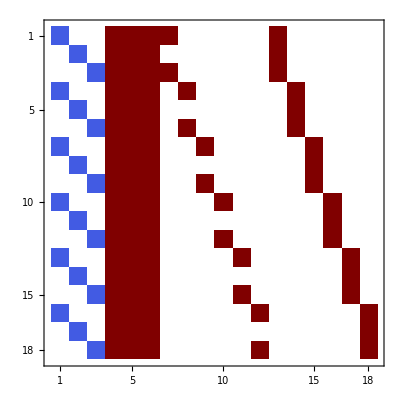

```mathematica
tempJ//MatrixPlot
```

```mathematica
?Rationalize
```

Rationalize[x] converts an approximate number x to a nearby rational with small denominator. 
Rationalize[x,dx] yields the rational number with smallest denominator that lies within dx of x.

```mathematica
qnew = SetPrecision[qecdat[[1]],20]
```

Part::partd: Part specification qecdat⟦1⟧ is longer than depth of object.

qecdat⟦1⟧

```mathematica
(Inverse[tempJ/.qnewlist]-Inverse[tempJ/.qnewlist])//MatrixForm
```

ReplaceAll::reps: {qnewlist} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

0

```mathematica
PseudoInverse[tempJ/.qnewlist]//MatrixForm
```

ReplaceAll::reps: {qnewlist} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

PseudoInverse[{{-1,0,0,(2 c1 (c1 c2-c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(c1 (1+c1^2-c2^2-c3^2) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),(2 c2 (c1 c2-c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(c2 (1+c1^2-c2^2-c3^2) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c2 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),(2 (c1 c2-c3) c3 Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+Cos[1/5+π/6]/(1+c1^2+c2^2+c3^2)+(c3 (1+c1^2-c2^2-c3^2) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c3 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),l1 Cos[ϕ1] Cos[ψ1],0,0,0,0,0,-l1 Sin[ϕ1] Sin[ψ1],0,0,0,0,0},{0,-1,0,-(c1 (-1+c1^2-c2^2+c3^2) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c1 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(2 c1 (c1 c2+c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),-(c2 (-1+c1^2-c2^2+c3^2) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(2 c2 (c1 c2+c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),-(c3 (-1+c1^2-c2^2+c3^2) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c3 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(2 c3 (c1 c2+c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-Sin[1/5+π/6]/(1+c1^2+c2^2+c3^2),0,0,0,0,0,0,-l1 Cos[ψ1],0,0,0,0,0},{0,0,-1,(2 c1 (c1+c2 c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-Cos[1/5+π/6]/(1+c1^2+c2^2+c3^2)-(2 c1 (c2-c1 c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c3 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),(2 c2 (c1+c2 c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c3 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)-(2 c2 (c2-c1 c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+Sin[1/5+π/6]/(1+c1^2+c2^2+c3^2),(2 c3 (c1+c2 c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)-(2 c3 (c2-c1 c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),-l1 Cos[ψ1] Sin[ϕ1],0,0,0,0,0,-l1 Cos[ϕ1] Sin[ψ1],0,0,0,0,0},{-1,0,0,(c1 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c2 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c1 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)+(c1 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),(c2 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c1 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c2 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)-(c2 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),((c1 c2-c3) c3 (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(√3 Cos[1/5]+Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-(c3 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)-(c3 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),0,l2 Cos[ϕ2] Cos[ψ2],0,0,0,0,0,-l2 Sin[ϕ2] Sin[ψ2],0,0,0,0},{0,-1,0,-(c1 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)+(c1 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c1 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c2 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),-(c2 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)-(c2 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c2 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c1 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),-(c3 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)+(c3 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c3 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(-Cos[1/5]+√3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,-l2 Cos[ψ2],0,0,0,0},{0,0,-1,-(4 c1 z+√3 Cos[1/5]+c3 Cos[1/5]-4 c1 l2 Cos[ϕ2] Cos[ψ2]+Sin[1/5]-√3 c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+1/((1+c1^2+c2^2+c3^2)^2)c1 (2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]-c2 Cos[1/5]+c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]-2 (1+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]+c1 Sin[1/5]+√3 c2 Sin[1/5]-√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),-(4 c2 z-Cos[1/5]+√3 c3 Cos[1/5]-4 c2 l2 Cos[ϕ2] Cos[ψ2]+√3 Sin[1/5]+c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+1/((1+c1^2+c2^2+c3^2)^2)c2 (2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]-c2 Cos[1/5]+c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]-2 (1+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]+c1 Sin[1/5]+√3 c2 Sin[1/5]-√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),-(4 c3 z+c1 Cos[1/5]+√3 c2 Cos[1/5]-4 c3 l2 Cos[ϕ2] Cos[ψ2]-√3 c1 Sin[1/5]+c2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+1/((1+c1^2+c2^2+c3^2)^2)c3 (2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]-c2 Cos[1/5]+c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]-2 (1+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]+c1 Sin[1/5]+√3 c2 Sin[1/5]-√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),0,-l2 Cos[ψ2] Sin[ϕ2],0,0,0,0,0,-l2 Cos[ϕ2] Sin[ψ2],0,0,0,0},{-1,0,0,1/2 (-(2 c1 (1+c1^2-c2^2-c3^2) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c1 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(4 c1 (-c1 c2+c3) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c2 (1+c1^2-c2^2-c3^2) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c2 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(4 c2 (-c1 c2+c3) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c1 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c3 (1+c1^2-c2^2-c3^2) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c3 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(4 c3 (-c1 c2+c3) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 Sin[1/5])/(1+c1^2+c2^2+c3^2)),0,0,l3 Cos[ϕ3] Cos[ψ3],0,0,0,0,0,-l3 Sin[ϕ3] Sin[ψ3],0,0,0},{0,-1,0,1/2 (-(4 c1 (c1 c2+c3) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c2 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(2 c1 (-1+c1^2-c2^2+c3^2) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c1 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(4 c2 (c1 c2+c3) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c1 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(2 c2 (-1+c1^2-c2^2+c3^2) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(4 c3 (c1 c2+c3) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(2 c3 (-1+c1^2-c2^2+c3^2) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c3 Sin[1/5])/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,0,-l3 Cos[ψ3],0,0,0},{0,0,-1,-(2 c1 z-c3 Cos[1/5]-2 c1 l3 Cos[ϕ3] Cos[ψ3]+Sin[1/5])/(1+c1^2+c2^2+c3^2)+(2 c1 ((1+c1^2+c2^2+c3^2) z+c2 Cos[1/5]-c1 c3 Cos[1/5]-(1+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(2 c2 z+Cos[1/5]-2 c2 l3 Cos[ϕ3] Cos[ψ3]+c3 Sin[1/5])/(1+c1^2+c2^2+c3^2)+(2 c2 ((1+c1^2+c2^2+c3^2) z+c2 Cos[1/5]-c1 c3 Cos[1/5]-(1+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(2 c3 z-c1 Cos[1/5]-2 c3 l3 Cos[ϕ3] Cos[ψ3]+c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)+(2 c3 ((1+c1^2+c2^2+c3^2) z+c2 Cos[1/5]-c1 c3 Cos[1/5]-(1+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),0,0,-l3 Cos[ψ3] Sin[ϕ3],0,0,0,0,0,-l3 Cos[ϕ3] Sin[ψ3],0,0,0},{-1,0,0,-(4 c1 x+2 c1 (-Cos[1/5]+2 Cos[1/3])-2 c2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+(c1 (2 (1+c1^2+c2^2+c3^2) x-Cos[1/5]+c2^2 Cos[1/5]+c3^2 Cos[1/5]+2 Cos[1/3]+2 c2^2 Cos[1/3]+2 c3^2 Cos[1/3]+c1^2 (-Cos[1/5]+2 Cos[1/3])-2 c1 c2 Sin[1/5]+2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(4 c2 x+2 c2 Cos[1/5]+4 c2 Cos[1/3]-2 c1 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+(c2 (2 (1+c1^2+c2^2+c3^2) x-Cos[1/5]+c2^2 Cos[1/5]+c3^2 Cos[1/5]+2 Cos[1/3]+2 c2^2 Cos[1/3]+2 c3^2 Cos[1/3]+c1^2 (-Cos[1/5]+2 Cos[1/3])-2 c1 c2 Sin[1/5]+2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(4 c3 x+2 c3 Cos[1/5]+4 c3 Cos[1/3]+2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+(c3 (2 (1+c1^2+c2^2+c3^2) x-Cos[1/5]+c2^2 Cos[1/5]+c3^2 Cos[1/5]+2 Cos[1/3]+2 c2^2 Cos[1/3]+2 c3^2 Cos[1/3]+c1^2 (-Cos[1/5]+2 Cos[1/3])-2 c1 c2 Sin[1/5]+2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),0,0,0,l4 Cos[ϕ4] Cos[ψ4],0,0,0,0,0,-l4 Sin[ϕ4] Sin[ψ4],0,0},{0,-1,0,(-4 c1 y+2 c2 Cos[1/5]-2 c1 (Sin[1/5]+2 Sin[1/3]))/(2 (1+c1^2+c2^2+c3^2))-(c1 (-2 (1+c1^2+c2^2+c3^2) y+2 c1 c2 Cos[1/5]+2 c3 Cos[1/5]+Sin[1/5]+c2^2 Sin[1/5]-c3^2 Sin[1/5]-2 Sin[1/3]-2 c2^2 Sin[1/3]-2 c3^2 Sin[1/3]-c1^2 (Sin[1/5]+2 Sin[1/3])))/((1+c1^2+c2^2+c3^2)^2),(-4 c2 y+2 c1 Cos[1/5]+2 c2 Sin[1/5]-4 c2 Sin[1/3])/(2 (1+c1^2+c2^2+c3^2))-(c2 (-2 (1+c1^2+c2^2+c3^2) y+2 c1 c2 Cos[1/5]+2 c3 Cos[1/5]+Sin[1/5]+c2^2 Sin[1/5]-c3^2 Sin[1/5]-2 Sin[1/3]-2 c2^2 Sin[1/3]-2 c3^2 Sin[1/3]-c1^2 (Sin[1/5]+2 Sin[1/3])))/((1+c1^2+c2^2+c3^2)^2),(-4 c3 y+2 Cos[1/5]-2 c3 Sin[1/5]-4 c3 Sin[1/3])/(2 (1+c1^2+c2^2+c3^2))-(c3 (-2 (1+c1^2+c2^2+c3^2) y+2 c1 c2 Cos[1/5]+2 c3 Cos[1/5]+Sin[1/5]+c2^2 Sin[1/5]-c3^2 Sin[1/5]-2 Sin[1/3]-2 c2^2 Sin[1/3]-2 c3^2 Sin[1/3]-c1^2 (Sin[1/5]+2 Sin[1/3])))/((1+c1^2+c2^2+c3^2)^2),0,0,0,0,0,0,0,0,0,-l4 Cos[ψ4],0,0},{0,0,-1,(-2 c1 z+c3 Cos[1/5]+2 c1 l4 Cos[ϕ4] Cos[ψ4]+Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c1 (-(1+c1^2+c2^2+c3^2) z-c2 Cos[1/5]+c1 c3 Cos[1/5]+(1+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),(-2 c2 z-Cos[1/5]+2 c2 l4 Cos[ϕ4] Cos[ψ4]+c3 Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c2 (-(1+c1^2+c2^2+c3^2) z-c2 Cos[1/5]+c1 c3 Cos[1/5]+(1+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),(-2 c3 z+c1 Cos[1/5]+2 c3 l4 Cos[ϕ4] Cos[ψ4]+c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c3 (-(1+c1^2+c2^2+c3^2) z-c2 Cos[1/5]+c1 c3 Cos[1/5]+(1+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),0,0,0,-l4 Cos[ψ4] Sin[ϕ4],0,0,0,0,0,-l4 Cos[ϕ4] Sin[ψ4],0,0},{-1,0,0,1/4 (-(4 c1 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c1 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 c2 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c2 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c2 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 (c1 c2-c3) c3 (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c3 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c3 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,l5 Cos[ϕ5] Cos[ψ5],0,0,0,0,0,-l5 Sin[ϕ5] Sin[ψ5],0},{0,-1,0,1/4 ((2 c1 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(4 c1 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c2 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(4 c2 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c3 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c3 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(4 c3 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,0,0,0,-l5 Cos[ψ5],0},{0,0,-1,(-4 c1 z+√3 Cos[1/5]-c3 Cos[1/5]+4 c1 l5 Cos[ϕ5] Cos[ψ5]+Sin[1/5]+√3 c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-1/((1+c1^2+c2^2+c3^2)^2)c1 (-2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]+c2 Cos[1/5]-c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]+2 (1+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]+c1 Sin[1/5]-√3 c2 Sin[1/5]+√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),(-4 c2 z+Cos[1/5]+√3 c3 Cos[1/5]+4 c2 l5 Cos[ϕ5] Cos[ψ5]-√3 Sin[1/5]+c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-1/((1+c1^2+c2^2+c3^2)^2)c2 (-2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]+c2 Cos[1/5]-c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]+2 (1+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]+c1 Sin[1/5]-√3 c2 Sin[1/5]+√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),(-4 c3 z-c1 Cos[1/5]+√3 c2 Cos[1/5]+4 c3 l5 Cos[ϕ5] Cos[ψ5]+√3 c1 Sin[1/5]+c2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-1/((1+c1^2+c2^2+c3^2)^2)c3 (-2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]+c2 Cos[1/5]-c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]+2 (1+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]+c1 Sin[1/5]-√3 c2 Sin[1/5]+√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),0,0,0,0,-l5 Cos[ψ5] Sin[ϕ5],0,0,0,0,0,-l5 Cos[ϕ5] Sin[ψ5],0},{-1,0,0,1/4 (-(4 c1 (c1 c2-c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(2 c1 (1+c1^2-c2^2-c3^2) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 c2 (c1 c2-c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(2 c2 (1+c1^2-c2^2-c3^2) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 (c1 c2-c3) c3 (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(2 c3 (1+c1^2-c2^2-c3^2) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c3 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,l6 Cos[ϕ6] Cos[ψ6],0,0,0,0,0,-l6 Sin[ϕ6] Sin[ψ6]},{0,-1,0,1/4 ((2 c1 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(4 c1 (c1 c2+c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c2 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c2 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(4 c2 (c1 c2+c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c3 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c3 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(4 c3 (c1 c2+c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,0,0,0,0,-l6 Cos[ψ6]},{0,0,-1,1/2 (-(2 c1 (c1+c2 c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(√3 Cos[1/5]-Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c1 (c2-c1 c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c3 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c2 (c1+c2 c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c3 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c2 (c2-c1 c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(Cos[1/5]+√3 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c3 (c1+c2 c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c3 (c2-c1 c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c1 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,-l6 Cos[ψ6] Sin[ϕ6],0,0,0,0,0,-l6 Cos[ϕ6] Sin[ψ6]}}/.qnewlist]

```mathematica
PseudoInverse[N[tempJ/.test]]
```

{{-0.158805,0.00539665,-0.000266726,-0.158805,0.00539665,-0.000266726,-0.158805,0.00539665,-0.000266726,-0.158805,0.00539665,-0.000266726,-0.158805,0.00539665,-0.000266726,-0.158805,0.00539665,-0.000266726},{0.00539665,-0.158912,0.00545441,0.00539665,-0.158912,0.00545441,0.00539665,-0.158912,0.00545441,0.00539665,-0.158912,0.00545441,0.00539665,-0.158912,0.00545441,0.00539665,-0.158912,0.00545441},{-0.000266726,0.00545441,-0.158811,-0.000266726,0.00545441,-0.158811,-0.000266726,0.00545441,-0.158811,-0.000266726,0.00545441,-0.158811,-0.000266726,0.00545441,-0.158811,-0.000266726,0.00545441,-0.158811},{-0.344909,0.412053,-0.27318,-0.411949,0.505322,-0.352959,-0.0371855,0.0737307,-0.0887887,0.129202,-0.133951,0.0610211,0.382094,-0.485783,0.361969,0.282746,-0.371371,0.291938},{-0.00378413,-0.140169,0.146191,-0.217302,0.158129,-0.0935245,-0.473614,0.708861,-0.580534,-0.328043,0.556559,-0.469922,0.477398,-0.568692,0.434343,0.545345,-0.714688,0.563446},{0.301747,0.0350036,-0.168795,0.186882,0.20312,-0.209371,-0.353349,0.362516,-0.0354723,-0.381697,0.236655,0.0512037,0.0516019,-0.397519,0.204267,0.194814,-0.439774,0.158168},{0.768914,-0.00448067,-0.926412,-0.490449,-0.0424813,0.292389,-0.0525496,-0.0830557,0.045191,0.0409697,-0.0558111,0.0292109,-0.0441524,0.0875364,0.216128,-0.160237,0.0982925,0.281659},{-0.486113,0.0278527,0.296771,0.774193,0.0530083,-1.05426,-0.159543,0.0469066,-0.0138218,-0.0456187,0.0201335,0.00843521,0.0359405,-0.0747594,0.32031,-0.0563631,-0.0731418,0.38073},{-0.0429085,0.0733598,0.0549354,-0.148496,0.226142,-0.00265584,0.791856,0.31597,-1.14792,-0.475035,0.187001,0.210648,-0.0767356,-0.38933,0.427896,0.0138145,-0.413143,0.395267},{0.0476821,0.0530901,0.0359952,-0.0359776,0.176549,0.0181795,-0.4707,0.257335,0.21503,0.779645,0.155292,-0.983323,-0.186698,-0.310425,0.352234,-0.0714559,-0.331841,0.30005},{-0.0537936,-0.0688791,0.206384,0.0292281,-0.183661,0.313526,-0.0670945,-0.232914,0.43764,-0.175651,-0.13119,0.3634,0.7931,0.301793,-1.30912,-0.463293,0.31485,-0.0736668},{-0.171285,-0.0809428,0.270493,-0.0660042,-0.229557,0.370985,0.020527,-0.304241,0.402051,-0.0618147,-0.175425,0.309795,-0.458958,0.385184,-0.0692852,0.800031,0.404983,-1.34587},{-0.371698,-0.840754,-0.547688,0.250015,0.0903698,0.108098,0.014307,0.203902,0.131244,-0.0357514,0.214147,0.122522,0.0111251,0.13926,0.0664717,0.0736101,0.109164,0.0603356},{0.255654,0.15887,0.0051249,-0.36654,-0.765716,-0.583359,0.0707114,0.101479,0.243418,0.00657132,0.103108,0.240242,-0.0384917,0.153332,0.0424119,0.0137025,0.165017,-0.00685585},{0.0268474,0.356239,-0.0977562,0.0850814,0.27604,-0.0189916,-0.386253,-1.02257,-0.305595,0.232812,-0.133786,0.350498,0.0131396,0.168744,0.0533787,-0.0300194,0.271426,-0.0405508},{-0.0270204,0.320209,-0.0369153,0.0191117,0.255445,0.0112417,0.238451,-0.0652859,0.247525,-0.383676,-0.996818,-0.378922,0.0764435,0.158758,0.0803457,0.0182978,0.243782,0.0177083},{-0.00141533,-0.0130766,0.295472,-0.0472226,0.0472704,0.201849,0.02568,0.321081,-0.175622,0.0908134,0.333319,-0.182064,-0.370531,-0.805595,-0.469823,0.244283,0.0330908,0.27117},{0.0592402,-0.0653982,0.322746,0.00116213,0.0126796,0.222145,-0.0212884,0.377488,-0.199988,0.0308382,0.396119,-0.211292,0.249922,0.101591,0.168198,-0.378267,-0.90639,-0.360825}}

```mathematica
Inverse[tempJ/.qnewlist]//MatrixForm
```

ReplaceAll::reps: {qnewlist} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Inverse[{{-1,0,0,(2 c1 (c1 c2-c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(c1 (1+c1^2-c2^2-c3^2) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),(2 c2 (c1 c2-c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(c2 (1+c1^2-c2^2-c3^2) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c2 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),(2 (c1 c2-c3) c3 Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+Cos[1/5+π/6]/(1+c1^2+c2^2+c3^2)+(c3 (1+c1^2-c2^2-c3^2) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c3 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),l1 Cos[ϕ1] Cos[ψ1],0,0,0,0,0,-l1 Sin[ϕ1] Sin[ψ1],0,0,0,0,0},{0,-1,0,-(c1 (-1+c1^2-c2^2+c3^2) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c1 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(2 c1 (c1 c2+c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),-(c2 (-1+c1^2-c2^2+c3^2) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(2 c2 (c1 c2+c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),-(c3 (-1+c1^2-c2^2+c3^2) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+(c3 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)+(2 c3 (c1 c2+c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-Sin[1/5+π/6]/(1+c1^2+c2^2+c3^2),0,0,0,0,0,0,-l1 Cos[ψ1],0,0,0,0,0},{0,0,-1,(2 c1 (c1+c2 c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-Cos[1/5+π/6]/(1+c1^2+c2^2+c3^2)-(2 c1 (c2-c1 c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c3 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),(2 c2 (c1+c2 c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c3 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)-(2 c2 (c2-c1 c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)+Sin[1/5+π/6]/(1+c1^2+c2^2+c3^2),(2 c3 (c1+c2 c3) Cos[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c2 Cos[1/5+π/6])/(1+c1^2+c2^2+c3^2)-(2 c3 (c2-c1 c3) Sin[1/5+π/6])/((1+c1^2+c2^2+c3^2)^2)-(c1 Sin[1/5+π/6])/(1+c1^2+c2^2+c3^2),-l1 Cos[ψ1] Sin[ϕ1],0,0,0,0,0,-l1 Cos[ϕ1] Sin[ψ1],0,0,0,0,0},{-1,0,0,(c1 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c2 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c1 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)+(c1 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),(c2 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c1 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c2 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)-(c2 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),((c1 c2-c3) c3 (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(√3 Cos[1/5]+Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-(c3 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)-(c3 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),0,l2 Cos[ϕ2] Cos[ψ2],0,0,0,0,0,-l2 Sin[ϕ2] Sin[ψ2],0,0,0,0},{0,-1,0,-(c1 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)+(c1 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c1 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c2 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),-(c2 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)-(c2 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c2 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c1 (-Cos[1/5]+√3 Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)),-(c3 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2)^2)+(c3 (√3 Cos[1/5]+Sin[1/5]))/(2 (1+c1^2+c2^2+c3^2))-(c3 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(-Cos[1/5]+√3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,-l2 Cos[ψ2],0,0,0,0},{0,0,-1,-(4 c1 z+√3 Cos[1/5]+c3 Cos[1/5]-4 c1 l2 Cos[ϕ2] Cos[ψ2]+Sin[1/5]-√3 c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+1/((1+c1^2+c2^2+c3^2)^2)c1 (2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]-c2 Cos[1/5]+c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]-2 (1+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]+c1 Sin[1/5]+√3 c2 Sin[1/5]-√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),-(4 c2 z-Cos[1/5]+√3 c3 Cos[1/5]-4 c2 l2 Cos[ϕ2] Cos[ψ2]+√3 Sin[1/5]+c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+1/((1+c1^2+c2^2+c3^2)^2)c2 (2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]-c2 Cos[1/5]+c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]-2 (1+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]+c1 Sin[1/5]+√3 c2 Sin[1/5]-√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),-(4 c3 z+c1 Cos[1/5]+√3 c2 Cos[1/5]-4 c3 l2 Cos[ϕ2] Cos[ψ2]-√3 c1 Sin[1/5]+c2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+1/((1+c1^2+c2^2+c3^2)^2)c3 (2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]-c2 Cos[1/5]+c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]-2 (1+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]+c1 Sin[1/5]+√3 c2 Sin[1/5]-√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),0,-l2 Cos[ψ2] Sin[ϕ2],0,0,0,0,0,-l2 Cos[ϕ2] Sin[ψ2],0,0,0,0},{-1,0,0,1/2 (-(2 c1 (1+c1^2-c2^2-c3^2) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c1 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(4 c1 (-c1 c2+c3) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c2 (1+c1^2-c2^2-c3^2) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c2 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(4 c2 (-c1 c2+c3) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c1 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c3 (1+c1^2-c2^2-c3^2) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c3 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(4 c3 (-c1 c2+c3) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 Sin[1/5])/(1+c1^2+c2^2+c3^2)),0,0,l3 Cos[ϕ3] Cos[ψ3],0,0,0,0,0,-l3 Sin[ϕ3] Sin[ψ3],0,0,0},{0,-1,0,1/2 (-(4 c1 (c1 c2+c3) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c2 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(2 c1 (-1+c1^2-c2^2+c3^2) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c1 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(4 c2 (c1 c2+c3) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c1 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(2 c2 (-1+c1^2-c2^2+c3^2) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)-(2 c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(4 c3 (c1 c2+c3) Cos[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 Cos[1/5])/(1+c1^2+c2^2+c3^2)-(2 c3 (-1+c1^2-c2^2+c3^2) Sin[1/5])/((1+c1^2+c2^2+c3^2)^2)+(2 c3 Sin[1/5])/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,0,-l3 Cos[ψ3],0,0,0},{0,0,-1,-(2 c1 z-c3 Cos[1/5]-2 c1 l3 Cos[ϕ3] Cos[ψ3]+Sin[1/5])/(1+c1^2+c2^2+c3^2)+(2 c1 ((1+c1^2+c2^2+c3^2) z+c2 Cos[1/5]-c1 c3 Cos[1/5]-(1+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(2 c2 z+Cos[1/5]-2 c2 l3 Cos[ϕ3] Cos[ψ3]+c3 Sin[1/5])/(1+c1^2+c2^2+c3^2)+(2 c2 ((1+c1^2+c2^2+c3^2) z+c2 Cos[1/5]-c1 c3 Cos[1/5]-(1+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(2 c3 z-c1 Cos[1/5]-2 c3 l3 Cos[ϕ3] Cos[ψ3]+c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)+(2 c3 ((1+c1^2+c2^2+c3^2) z+c2 Cos[1/5]-c1 c3 Cos[1/5]-(1+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),0,0,-l3 Cos[ψ3] Sin[ϕ3],0,0,0,0,0,-l3 Cos[ϕ3] Sin[ψ3],0,0,0},{-1,0,0,-(4 c1 x+2 c1 (-Cos[1/5]+2 Cos[1/3])-2 c2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+(c1 (2 (1+c1^2+c2^2+c3^2) x-Cos[1/5]+c2^2 Cos[1/5]+c3^2 Cos[1/5]+2 Cos[1/3]+2 c2^2 Cos[1/3]+2 c3^2 Cos[1/3]+c1^2 (-Cos[1/5]+2 Cos[1/3])-2 c1 c2 Sin[1/5]+2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(4 c2 x+2 c2 Cos[1/5]+4 c2 Cos[1/3]-2 c1 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+(c2 (2 (1+c1^2+c2^2+c3^2) x-Cos[1/5]+c2^2 Cos[1/5]+c3^2 Cos[1/5]+2 Cos[1/3]+2 c2^2 Cos[1/3]+2 c3^2 Cos[1/3]+c1^2 (-Cos[1/5]+2 Cos[1/3])-2 c1 c2 Sin[1/5]+2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),-(4 c3 x+2 c3 Cos[1/5]+4 c3 Cos[1/3]+2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))+(c3 (2 (1+c1^2+c2^2+c3^2) x-Cos[1/5]+c2^2 Cos[1/5]+c3^2 Cos[1/5]+2 Cos[1/3]+2 c2^2 Cos[1/3]+2 c3^2 Cos[1/3]+c1^2 (-Cos[1/5]+2 Cos[1/3])-2 c1 c2 Sin[1/5]+2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),0,0,0,l4 Cos[ϕ4] Cos[ψ4],0,0,0,0,0,-l4 Sin[ϕ4] Sin[ψ4],0,0},{0,-1,0,(-4 c1 y+2 c2 Cos[1/5]-2 c1 (Sin[1/5]+2 Sin[1/3]))/(2 (1+c1^2+c2^2+c3^2))-(c1 (-2 (1+c1^2+c2^2+c3^2) y+2 c1 c2 Cos[1/5]+2 c3 Cos[1/5]+Sin[1/5]+c2^2 Sin[1/5]-c3^2 Sin[1/5]-2 Sin[1/3]-2 c2^2 Sin[1/3]-2 c3^2 Sin[1/3]-c1^2 (Sin[1/5]+2 Sin[1/3])))/((1+c1^2+c2^2+c3^2)^2),(-4 c2 y+2 c1 Cos[1/5]+2 c2 Sin[1/5]-4 c2 Sin[1/3])/(2 (1+c1^2+c2^2+c3^2))-(c2 (-2 (1+c1^2+c2^2+c3^2) y+2 c1 c2 Cos[1/5]+2 c3 Cos[1/5]+Sin[1/5]+c2^2 Sin[1/5]-c3^2 Sin[1/5]-2 Sin[1/3]-2 c2^2 Sin[1/3]-2 c3^2 Sin[1/3]-c1^2 (Sin[1/5]+2 Sin[1/3])))/((1+c1^2+c2^2+c3^2)^2),(-4 c3 y+2 Cos[1/5]-2 c3 Sin[1/5]-4 c3 Sin[1/3])/(2 (1+c1^2+c2^2+c3^2))-(c3 (-2 (1+c1^2+c2^2+c3^2) y+2 c1 c2 Cos[1/5]+2 c3 Cos[1/5]+Sin[1/5]+c2^2 Sin[1/5]-c3^2 Sin[1/5]-2 Sin[1/3]-2 c2^2 Sin[1/3]-2 c3^2 Sin[1/3]-c1^2 (Sin[1/5]+2 Sin[1/3])))/((1+c1^2+c2^2+c3^2)^2),0,0,0,0,0,0,0,0,0,-l4 Cos[ψ4],0,0},{0,0,-1,(-2 c1 z+c3 Cos[1/5]+2 c1 l4 Cos[ϕ4] Cos[ψ4]+Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c1 (-(1+c1^2+c2^2+c3^2) z-c2 Cos[1/5]+c1 c3 Cos[1/5]+(1+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),(-2 c2 z-Cos[1/5]+2 c2 l4 Cos[ϕ4] Cos[ψ4]+c3 Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c2 (-(1+c1^2+c2^2+c3^2) z-c2 Cos[1/5]+c1 c3 Cos[1/5]+(1+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),(-2 c3 z+c1 Cos[1/5]+2 c3 l4 Cos[ϕ4] Cos[ψ4]+c2 Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c3 (-(1+c1^2+c2^2+c3^2) z-c2 Cos[1/5]+c1 c3 Cos[1/5]+(1+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]+c1 Sin[1/5]+c2 c3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2),0,0,0,-l4 Cos[ψ4] Sin[ϕ4],0,0,0,0,0,-l4 Cos[ϕ4] Sin[ψ4],0,0},{-1,0,0,1/4 (-(4 c1 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c1 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 c2 (c1 c2-c3) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c2 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c2 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 (c1 c2-c3) c3 (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c3 (1+c1^2-c2^2-c3^2) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c3 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,l5 Cos[ϕ5] Cos[ψ5],0,0,0,0,0,-l5 Sin[ϕ5] Sin[ψ5],0},{0,-1,0,1/4 ((2 c1 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(4 c1 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c2 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(4 c2 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c3 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]+Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c3 (√3 Cos[1/5]+Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(4 c3 (c1 c2+c3) (-Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 (-Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,0,0,0,-l5 Cos[ψ5],0},{0,0,-1,(-4 c1 z+√3 Cos[1/5]-c3 Cos[1/5]+4 c1 l5 Cos[ϕ5] Cos[ψ5]+Sin[1/5]+√3 c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-1/((1+c1^2+c2^2+c3^2)^2)c1 (-2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]+c2 Cos[1/5]-c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]+2 (1+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]+c1 Sin[1/5]-√3 c2 Sin[1/5]+√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),(-4 c2 z+Cos[1/5]+√3 c3 Cos[1/5]+4 c2 l5 Cos[ϕ5] Cos[ψ5]-√3 Sin[1/5]+c3 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-1/((1+c1^2+c2^2+c3^2)^2)c2 (-2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]+c2 Cos[1/5]-c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]+2 (1+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]+c1 Sin[1/5]-√3 c2 Sin[1/5]+√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),(-4 c3 z-c1 Cos[1/5]+√3 c2 Cos[1/5]+4 c3 l5 Cos[ϕ5] Cos[ψ5]+√3 c1 Sin[1/5]+c2 Sin[1/5])/(2 (1+c1^2+c2^2+c3^2))-1/((1+c1^2+c2^2+c3^2)^2)c3 (-2 (1+c1^2+c2^2+c3^2) z+√3 c1 Cos[1/5]+c2 Cos[1/5]-c1 c3 Cos[1/5]+√3 c2 c3 Cos[1/5]+2 (1+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]+c1 Sin[1/5]-√3 c2 Sin[1/5]+√3 c1 c3 Sin[1/5]+c2 c3 Sin[1/5]),0,0,0,0,-l5 Cos[ψ5] Sin[ϕ5],0,0,0,0,0,-l5 Cos[ϕ5] Sin[ψ5],0},{-1,0,0,1/4 (-(4 c1 (c1 c2-c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(2 c1 (1+c1^2-c2^2-c3^2) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 c2 (c1 c2-c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c1 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(2 c2 (1+c1^2-c2^2-c3^2) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 (-(4 (c1 c2-c3) c3 (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(2 c3 (1+c1^2-c2^2-c3^2) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c3 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,l6 Cos[ϕ6] Cos[ψ6],0,0,0,0,0,-l6 Sin[ϕ6] Sin[ψ6]},{0,-1,0,1/4 ((2 c1 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(4 c1 (c1 c2+c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c2 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c2 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(2 c2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(4 c2 (c1 c2+c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c1 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/4 ((2 c3 (-1+c1^2-c2^2+c3^2) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 c3 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)+(4 c3 (c1 c2+c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(2 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,0,0,0,0,0,0,-l6 Cos[ψ6]},{0,0,-1,1/2 (-(2 c1 (c1+c2 c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(√3 Cos[1/5]-Sin[1/5])/(1+c1^2+c2^2+c3^2)-(2 c1 (c2-c1 c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c3 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c2 (c1+c2 c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c3 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c2 (c2-c1 c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(Cos[1/5]+√3 Sin[1/5])/(1+c1^2+c2^2+c3^2)),1/2 (-(2 c3 (c1+c2 c3) (√3 Cos[1/5]-Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)+(c2 (√3 Cos[1/5]-Sin[1/5]))/(1+c1^2+c2^2+c3^2)-(2 c3 (c2-c1 c3) (Cos[1/5]+√3 Sin[1/5]))/((1+c1^2+c2^2+c3^2)^2)-(c1 (Cos[1/5]+√3 Sin[1/5]))/(1+c1^2+c2^2+c3^2)),0,0,0,0,0,-l6 Cos[ψ6] Sin[ϕ6],0,0,0,0,0,-l6 Cos[ϕ6] Sin[ψ6]}}/.qnewlist]

```mathematica
qnewlist = Inner[Rule, q, qnew, List];
```

Inner::heads: Heads Part and List at positions 3 and 2 are expected to be the same.

```mathematica
SingularValueList[tempJ/.qnewlist]//Dimensions
```

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},qecdat⟦1⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

{1}

```mathematica
lhsvec = -Inverse[N[tempJ/.qnewlist]].(Jηθ/.qnewlist).ConstantArray[1, {6}]
```

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},qecdat⟦1⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Inverse[{{-1.,0.,0.,(1.49886 c1 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(0.662086 c1 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(0.662086 c1)/(1.+c1^2+c2^2+c3^2)-(0.749428 c2)/(1.+c1^2+c2^2+c3^2),(1.49886 c2 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(0.662086 c2 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(0.749428 c1)/(1.+c1^2+c2^2+c3^2)+(0.662086 c2)/(1.+c1^2+c2^2+c3^2),(1.49886 (c1 c2-1. c3) c3)/((1.+c1^2+c2^2+c3^2)^2)+(0.662086 c3 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)+0.749428/(1.+c1^2+c2^2+c3^2)+(0.662086 c3)/(1.+c1^2+c2^2+c3^2),l1 Cos[ϕ1] Cos[ψ1],0.,0.,0.,0.,0.,-1. l1 Sin[ϕ1] Sin[ψ1],0.,0.,0.,0.,0.},{0.,-1.,0.,(1.32417 c1 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.749428 c1 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)+(0.749428 c1)/(1.+c1^2+c2^2+c3^2)-(0.662086 c2)/(1.+c1^2+c2^2+c3^2),(1.32417 c2 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.749428 c2 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(0.662086 c1)/(1.+c1^2+c2^2+c3^2)-(0.749428 c2)/(1.+c1^2+c2^2+c3^2),(1.32417 c3 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.749428 c3 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-0.662086/(1.+c1^2+c2^2+c3^2)+(0.749428 c3)/(1.+c1^2+c2^2+c3^2),0.,0.,0.,0.,0.,0.,-1. l1 Cos[ψ1],0.,0.,0.,0.,0.},{0.,0.,-1.,-(1.32417 c1 (c2-1. c1 c3))/((1.+c1^2+c2^2+c3^2)^2)+(1.49886 c1 (c1+c2 c3))/((1.+c1^2+c2^2+c3^2)^2)-0.749428/(1.+c1^2+c2^2+c3^2)-(0.662086 c3)/(1.+c1^2+c2^2+c3^2),-(1.32417 c2 (c2-1. c1 c3))/((1.+c1^2+c2^2+c3^2)^2)+(1.49886 c2 (c1+c2 c3))/((1.+c1^2+c2^2+c3^2)^2)+0.662086/(1.+c1^2+c2^2+c3^2)-(0.749428 c3)/(1.+c1^2+c2^2+c3^2),-(1.32417 c3 (c2-1. c1 c3))/((1.+c1^2+c2^2+c3^2)^2)+(1.49886 c3 (c1+c2 c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.662086 c1)/(1.+c1^2+c2^2+c3^2)-(0.749428 c2)/(1.+c1^2+c2^2+c3^2),-1. l1 Cos[ψ1] Sin[ϕ1],0.,0.,0.,0.,0.,-1. l1 Cos[ϕ1] Sin[ψ1],0.,0.,0.,0.,0.},{-1.,0.,0.,(1.89619 c1 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(0.317981 c1 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(0.317981 c1)/(1.+c1^2+c2^2+c3^2)-(0.948097 c2)/(1.+c1^2+c2^2+c3^2),(1.89619 c2 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(0.317981 c2 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(0.948097 c1)/(1.+c1^2+c2^2+c3^2)+(0.317981 c2)/(1.+c1^2+c2^2+c3^2),(1.89619 (c1 c2-1. c3) c3)/((1.+c1^2+c2^2+c3^2)^2)+(0.317981 c3 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)+0.948097/(1.+c1^2+c2^2+c3^2)+(0.317981 c3)/(1.+c1^2+c2^2+c3^2),0.,l2 Cos[ϕ2] Cos[ψ2],0.,0.,0.,0.,0.,-1. l2 Sin[ϕ2] Sin[ψ2],0.,0.,0.,0.},{0.,-1.,0.,(0.635961 c1 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.948097 c1 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)+(0.948097 c1)/(1.+c1^2+c2^2+c3^2)-(0.317981 c2)/(1.+c1^2+c2^2+c3^2),(0.635961 c2 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.948097 c2 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(0.317981 c1)/(1.+c1^2+c2^2+c3^2)-(0.948097 c2)/(1.+c1^2+c2^2+c3^2),(0.635961 c3 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.948097 c3 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-0.317981/(1.+c1^2+c2^2+c3^2)+(0.948097 c3)/(1.+c1^2+c2^2+c3^2),0.,0.,0.,0.,0.,0.,0.,-1. l2 Cos[ψ2],0.,0.,0.,0.},{0.,0.,-1.,-(0.5 (1.89619+0.635961 c3+4. c1 z-4. c1 l2 Cos[ϕ2] Cos[ψ2]))/(1.+c1^2+c2^2+c3^2)+(c1 (1.89619 c1-0.635961 c2+0.635961 c1 c3+1.89619 c2 c3+2. (1.+c1^2+c2^2+c3^2) z-2. (1.+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]))/((1.+c1^2+c2^2+c3^2)^2),-(0.5 (-0.635961+1.89619 c3+4. c2 z-4. c2 l2 Cos[ϕ2] Cos[ψ2]))/(1.+c1^2+c2^2+c3^2)+(c2 (1.89619 c1-0.635961 c2+0.635961 c1 c3+1.89619 c2 c3+2. (1.+c1^2+c2^2+c3^2) z-2. (1.+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]))/((1.+c1^2+c2^2+c3^2)^2),-(0.5 (0.635961 c1+1.89619 c2+4. c3 z-4. c3 l2 Cos[ϕ2] Cos[ψ2]))/(1.+c1^2+c2^2+c3^2)+(c3 (1.89619 c1-0.635961 c2+0.635961 c1 c3+1.89619 c2 c3+2. (1.+c1^2+c2^2+c3^2) z-2. (1.+c1^2+c2^2+c3^2) l2 Cos[ϕ2] Cos[ψ2]))/((1.+c1^2+c2^2+c3^2)^2),0.,-1. l2 Cos[ψ2] Sin[ϕ2],0.,0.,0.,0.,0.,-1. l2 Cos[ϕ2] Sin[ψ2],0.,0.,0.,0.},{-1.,0.,0.,0.5 (-(0.794677 c1 (-1. c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(1.96013 c1 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)+(1.96013 c1)/(1.+c1^2+c2^2+c3^2)-(0.397339 c2)/(1.+c1^2+c2^2+c3^2)),0.5 (-(0.794677 c2 (-1. c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(1.96013 c2 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(0.397339 c1)/(1.+c1^2+c2^2+c3^2)-(1.96013 c2)/(1.+c1^2+c2^2+c3^2)),0.5 (-(0.794677 c3 (-1. c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(1.96013 c3 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)+0.397339/(1.+c1^2+c2^2+c3^2)-(1.96013 c3)/(1.+c1^2+c2^2+c3^2)),0.,0.,l3 Cos[ϕ3] Cos[ψ3],0.,0.,0.,0.,0.,-1. l3 Sin[ϕ3] Sin[ψ3],0.,0.,0.},{0.,-1.,0.,0.5 (-(3.92027 c1 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.397339 c1 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)+(0.397339 c1)/(1.+c1^2+c2^2+c3^2)+(1.96013 c2)/(1.+c1^2+c2^2+c3^2)),0.5 (-(3.92027 c2 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.397339 c2 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)+(1.96013 c1)/(1.+c1^2+c2^2+c3^2)-(0.397339 c2)/(1.+c1^2+c2^2+c3^2)),0.5 (-(3.92027 c3 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)-(0.397339 c3 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)+1.96013/(1.+c1^2+c2^2+c3^2)+(0.397339 c3)/(1.+c1^2+c2^2+c3^2)),0.,0.,0.,0.,0.,0.,0.,0.,-1. l3 Cos[ψ3],0.,0.,0.},{0.,0.,-1.,-(1. (0.198669-0.980067 c3+2. c1 z-2. c1 l3 Cos[ϕ3] Cos[ψ3]))/(1.+c1^2+c2^2+c3^2)+(2. c1 (0.198669 c1+0.980067 c2-0.980067 c1 c3+0.198669 c2 c3+(1.+c1^2+c2^2+c3^2) z-1. (1.+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]))/((1.+c1^2+c2^2+c3^2)^2),-(1. (0.980067+0.198669 c3+2. c2 z-2. c2 l3 Cos[ϕ3] Cos[ψ3]))/(1.+c1^2+c2^2+c3^2)+(2. c2 (0.198669 c1+0.980067 c2-0.980067 c1 c3+0.198669 c2 c3+(1.+c1^2+c2^2+c3^2) z-1. (1.+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]))/((1.+c1^2+c2^2+c3^2)^2),-(1. (-0.980067 c1+0.198669 c2+2. c3 z-2. c3 l3 Cos[ϕ3] Cos[ψ3]))/(1.+c1^2+c2^2+c3^2)+(2. c3 (0.198669 c1+0.980067 c2-0.980067 c1 c3+0.198669 c2 c3+(1.+c1^2+c2^2+c3^2) z-1. (1.+c1^2+c2^2+c3^2) l3 Cos[ϕ3] Cos[ψ3]))/((1.+c1^2+c2^2+c3^2)^2),0.,0.,-1. l3 Cos[ψ3] Sin[ϕ3],0.,0.,0.,0.,0.,-1. l3 Cos[ϕ3] Sin[ψ3],0.,0.,0.},{-1.,0.,0.,-(0.5 (1.81969 c1-0.397339 c2+4. c1 x))/(1.+c1^2+c2^2+c3^2)+(c1 (0.909847+0.909847 c1^2-0.397339 c1 c2+2.86998 c2^2+0.397339 c3+2.86998 c3^2+2. (1.+c1^2+c2^2+c3^2) x))/((1.+c1^2+c2^2+c3^2)^2),-(0.5 (-0.397339 c1+5.73996 c2+4. c2 x))/(1.+c1^2+c2^2+c3^2)+(c2 (0.909847+0.909847 c1^2-0.397339 c1 c2+2.86998 c2^2+0.397339 c3+2.86998 c3^2+2. (1.+c1^2+c2^2+c3^2) x))/((1.+c1^2+c2^2+c3^2)^2),-(0.5 (0.397339+5.73996 c3+4. c3 x))/(1.+c1^2+c2^2+c3^2)+(c3 (0.909847+0.909847 c1^2-0.397339 c1 c2+2.86998 c2^2+0.397339 c3+2.86998 c3^2+2. (1.+c1^2+c2^2+c3^2) x))/((1.+c1^2+c2^2+c3^2)^2),0.,0.,0.,l4 Cos[ϕ4] Cos[ψ4],0.,0.,0.,0.,0.,-1. l4 Sin[ϕ4] Sin[ψ4],0.,0.},{0.,-1.,0.,(0.5 (-1.70612 c1+1.96013 c2-4. c1 y))/(1.+c1^2+c2^2+c3^2)-(1. c1 (-0.45572-0.853059 c1^2+1.96013 c1 c2-0.45572 c2^2+1.96013 c3-0.853059 c3^2-2. (1.+c1^2+c2^2+c3^2) y))/((1.+c1^2+c2^2+c3^2)^2),(0.5 (1.96013 c1-0.91144 c2-4. c2 y))/(1.+c1^2+c2^2+c3^2)-(1. c2 (-0.45572-0.853059 c1^2+1.96013 c1 c2-0.45572 c2^2+1.96013 c3-0.853059 c3^2-2. (1.+c1^2+c2^2+c3^2) y))/((1.+c1^2+c2^2+c3^2)^2),(0.5 (1.96013-1.70612 c3-4. c3 y))/(1.+c1^2+c2^2+c3^2)-(1. c3 (-0.45572-0.853059 c1^2+1.96013 c1 c2-0.45572 c2^2+1.96013 c3-0.853059 c3^2-2. (1.+c1^2+c2^2+c3^2) y))/((1.+c1^2+c2^2+c3^2)^2),0.,0.,0.,0.,0.,0.,0.,0.,0.,-1. l4 Cos[ψ4],0.,0.},{0.,0.,-1.,(0.198669+0.980067 c3-2. c1 z+2. c1 l4 Cos[ϕ4] Cos[ψ4])/(1.+c1^2+c2^2+c3^2)-(2. c1 (0.198669 c1-0.980067 c2+0.980067 c1 c3+0.198669 c2 c3-1. (1.+c1^2+c2^2+c3^2) z+(1.+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]))/((1.+c1^2+c2^2+c3^2)^2),(-0.980067+0.198669 c3-2. c2 z+2. c2 l4 Cos[ϕ4] Cos[ψ4])/(1.+c1^2+c2^2+c3^2)-(2. c2 (0.198669 c1-0.980067 c2+0.980067 c1 c3+0.198669 c2 c3-1. (1.+c1^2+c2^2+c3^2) z+(1.+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]))/((1.+c1^2+c2^2+c3^2)^2),(0.980067 c1+0.198669 c2-2. c3 z+2. c3 l4 Cos[ϕ4] Cos[ψ4])/(1.+c1^2+c2^2+c3^2)-(2. c3 (0.198669 c1-0.980067 c2+0.980067 c1 c3+0.198669 c2 c3-1. (1.+c1^2+c2^2+c3^2) z+(1.+c1^2+c2^2+c3^2) l4 Cos[ϕ4] Cos[ψ4]))/((1.+c1^2+c2^2+c3^2)^2),0.,0.,0.,-1. l4 Cos[ψ4] Sin[ϕ4],0.,0.,0.,0.,0.,-1. l4 Cos[ϕ4] Sin[ψ4],0.,0.},{-1.,0.,0.,0.25 (-(7.58478 c1 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(1.27192 c1 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(1.27192 c1)/(1.+c1^2+c2^2+c3^2)+(3.79239 c2)/(1.+c1^2+c2^2+c3^2)),0.25 (-(7.58478 c2 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(1.27192 c2 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)+(3.79239 c1)/(1.+c1^2+c2^2+c3^2)+(1.27192 c2)/(1.+c1^2+c2^2+c3^2)),0.25 (-(7.58478 (c1 c2-1. c3) c3)/((1.+c1^2+c2^2+c3^2)^2)+(1.27192 c3 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-3.79239/(1.+c1^2+c2^2+c3^2)+(1.27192 c3)/(1.+c1^2+c2^2+c3^2)),0.,0.,0.,0.,l5 Cos[ϕ5] Cos[ψ5],0.,0.,0.,0.,0.,-1. l5 Sin[ϕ5] Sin[ψ5],0.},{0.,-1.,0.,0.25 ((2.54384 c1 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)+(3.79239 c1 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(3.79239 c1)/(1.+c1^2+c2^2+c3^2)-(1.27192 c2)/(1.+c1^2+c2^2+c3^2)),0.25 ((2.54384 c2 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)+(3.79239 c2 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(1.27192 c1)/(1.+c1^2+c2^2+c3^2)+(3.79239 c2)/(1.+c1^2+c2^2+c3^2)),0.25 ((2.54384 c3 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)+(3.79239 c3 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-1.27192/(1.+c1^2+c2^2+c3^2)-(3.79239 c3)/(1.+c1^2+c2^2+c3^2)),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1. l5 Cos[ψ5],0.},{0.,0.,-1.,(0.5 (1.89619-0.635961 c3-4. c1 z+4. c1 l5 Cos[ϕ5] Cos[ψ5]))/(1.+c1^2+c2^2+c3^2)-(1. c1 (1.89619 c1+0.635961 c2-0.635961 c1 c3+1.89619 c2 c3-2. (1.+c1^2+c2^2+c3^2) z+2. (1.+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]))/((1.+c1^2+c2^2+c3^2)^2),(0.5 (0.635961+1.89619 c3-4. c2 z+4. c2 l5 Cos[ϕ5] Cos[ψ5]))/(1.+c1^2+c2^2+c3^2)-(1. c2 (1.89619 c1+0.635961 c2-0.635961 c1 c3+1.89619 c2 c3-2. (1.+c1^2+c2^2+c3^2) z+2. (1.+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]))/((1.+c1^2+c2^2+c3^2)^2),(0.5 (-0.635961 c1+1.89619 c2-4. c3 z+4. c3 l5 Cos[ϕ5] Cos[ψ5]))/(1.+c1^2+c2^2+c3^2)-(1. c3 (1.89619 c1+0.635961 c2-0.635961 c1 c3+1.89619 c2 c3-2. (1.+c1^2+c2^2+c3^2) z+2. (1.+c1^2+c2^2+c3^2) l5 Cos[ϕ5] Cos[ψ5]))/((1.+c1^2+c2^2+c3^2)^2),0.,0.,0.,0.,-1. l5 Cos[ψ5] Sin[ϕ5],0.,0.,0.,0.,0.,-1. l5 Cos[ϕ5] Sin[ψ5],0.},{-1.,0.,0.,0.25 (-(5.99542 c1 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(2.64834 c1 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(2.64834 c1)/(1.+c1^2+c2^2+c3^2)+(2.99771 c2)/(1.+c1^2+c2^2+c3^2)),0.25 (-(5.99542 c2 (c1 c2-1. c3))/((1.+c1^2+c2^2+c3^2)^2)+(2.64834 c2 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)+(2.99771 c1)/(1.+c1^2+c2^2+c3^2)+(2.64834 c2)/(1.+c1^2+c2^2+c3^2)),0.25 (-(5.99542 (c1 c2-1. c3) c3)/((1.+c1^2+c2^2+c3^2)^2)+(2.64834 c3 (1.+c1^2-1. c2^2-1. c3^2))/((1.+c1^2+c2^2+c3^2)^2)-2.99771/(1.+c1^2+c2^2+c3^2)+(2.64834 c3)/(1.+c1^2+c2^2+c3^2)),0.,0.,0.,0.,0.,l6 Cos[ϕ6] Cos[ψ6],0.,0.,0.,0.,0.,-1. l6 Sin[ϕ6] Sin[ψ6]},{0.,-1.,0.,0.25 ((5.29669 c1 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)+(2.99771 c1 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(2.99771 c1)/(1.+c1^2+c2^2+c3^2)-(2.64834 c2)/(1.+c1^2+c2^2+c3^2)),0.25 ((5.29669 c2 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)+(2.99771 c2 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-(2.64834 c1)/(1.+c1^2+c2^2+c3^2)+(2.99771 c2)/(1.+c1^2+c2^2+c3^2)),0.25 ((5.29669 c3 (c1 c2+c3))/((1.+c1^2+c2^2+c3^2)^2)+(2.99771 c3 (-1.+c1^2-1. c2^2+c3^2))/((1.+c1^2+c2^2+c3^2)^2)-2.64834/(1.+c1^2+c2^2+c3^2)-(2.99771 c3)/(1.+c1^2+c2^2+c3^2)),0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,-1. l6 Cos[ψ6]},{0.,0.,-1.,0.5 (-(2.64834 c1 (c2-1. c1 c3))/((1.+c1^2+c2^2+c3^2)^2)-(2.99771 c1 (c1+c2 c3))/((1.+c1^2+c2^2+c3^2)^2)+1.49886/(1.+c1^2+c2^2+c3^2)-(1.32417 c3)/(1.+c1^2+c2^2+c3^2)),0.5 (-(2.64834 c2 (c2-1. c1 c3))/((1.+c1^2+c2^2+c3^2)^2)-(2.99771 c2 (c1+c2 c3))/((1.+c1^2+c2^2+c3^2)^2)+1.32417/(1.+c1^2+c2^2+c3^2)+(1.49886 c3)/(1.+c1^2+c2^2+c3^2)),0.5 (-(2.64834 c3 (c2-1. c1 c3))/((1.+c1^2+c2^2+c3^2)^2)-(2.99771 c3 (c1+c2 c3))/((1.+c1^2+c2^2+c3^2)^2)-(1.32417 c1)/(1.+c1^2+c2^2+c3^2)+(1.49886 c2)/(1.+c1^2+c2^2+c3^2)),0.,0.,0.,0.,0.,-1. l6 Cos[ψ6] Sin[ϕ6],0.,0.,0.,0.,0.,-1. l6 Cos[ϕ6] Sin[ψ6]}}/.Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},qecdat⟦1⟧,List]].(Jηθ/.Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},qecdat⟦1⟧,List]).{1,1,1,1,1,1}

```mathematica
(Jηθ/.qnewlist).ConstantArray[1, {6}]//MatrixForm
```

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},qecdat⟦1⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(Jηθ/.Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},qecdat⟦1⟧,List]).{1,1,1,1,1,1}

```mathematica
-N[tempJ/.qnewlist].lhsvec//MatrixForm
```

ReplaceAll::reps: {Inner[Rule,{x,y,z,c1,c2,c3,ϕ1,ϕ2,ϕ3,ϕ4,ϕ5,ϕ6,ψ1,ψ2,ψ3,ψ4,ψ5,ψ6,l1,l2,l3,l4,l5,l6},qecdat⟦1⟧,List]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-1
 |  |  |  |

```mathematica
SingularValueList[N[tempJ/.test, 50]]//Dimensions
```

{15}

```mathematica
MatrixRank[N[tempJ/.test]]
```

15

```mathematica
ctempJ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tempJ]];
```

```mathematica
als = {{al1x, al1y, 0}, {al2x, al2y, 0}, {al3x, al3y, 0}, {al4x, al4y, 0}, {al5x, al5y, 0}, {al6x, al6y, 0}};
bs = {{b1x, b1y, 0}, {b2x, b2y, 0}, {b3x, b3y, 0}, {b4x, b4y, 0}, {b5x, b5y, 0}, {b6x, b6y, 0}};

alsrules = Inner[Rule, Flatten[als[[;;, 1;;2]]], Flatten[al[[;;, 1;;2]]], List];
bsrules = Inner[Rule, Flatten[bs[[;;, 1;;2]]], Flatten[b[[;;, 1;;2]]], List];

atps = Table[pc+Rtp.als[[i]],{i,6}];
ajs = Table[bs[[i]]+Rl[[i]].{0,0,l[[i]]},{i, 6}];
```

```mathematica
Jηq = D[η, {qq}];
Jηx =D[η, {qx}];
```

```mathematica
dϕ = Table[Symbol["dϕ"<>ToString[i]],{i, 6}];
dψ = Table[Symbol["dψ"<>ToString[i]],{i, 6}];
dl = Table[Symbol["dl"<>ToString[i]],{i, 6}];
dq = Join[dϕ, dψ,dl];
dqrule = Inner[Rule, D[qq/.qrule, t], dq, List];
rqϕrule= Join[Inner[Rule,qq/.qrule, qq, List], dqrule];
rxrule = Inner[Rule, qx/.qrule, qx, List];
drxrule = Inner[Rule, D[qx/.qrule, t], {dx, dy, dz, dc1, dc2, dc3}, List];
rqrule = Join[rxrule, drxrule, rqϕrule];
```

```mathematica
cJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηq]];
```

```mathematica
dJηq = D[Jηq/.qrule, t]/.rqrule;
cdJηq = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηq]];
```

```mathematica
cJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[Jηx]];
```

```mathematica
dJηx = D[Jηx/.qrule, t]/.rqrule;
cdJηx = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηx]];
```

```mathematica
tMmat = TrigExpand[Mmat/.rqrule];
cMmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tMmat]];
```

```mathematica
tCmat = TrigExpand[Simplify[tempC/.rqrule]];
cCmat = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[tCmat]];
```

```mathematica
cGvec = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[G]];
```

```mathematica
(*IK module for the manipulator*)
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

```mathematica
samplex = Inner[Rule, qx, {0,0,0.75,0,0,0}, List];
```

```mathematica
li2 = Table[(atp-bs)[[i]].(atp-bs)[[i]],{i, 6}];
li = Sqrt[Together[li2]];
lirule = Inner[Rule, l, li,List];
```

```mathematica
lval = Inner[Rule, l, Simplify[li/.alsrules/.bsrules/.datap], List];
clval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}}, Evaluate[l/.lval]];
```

```mathematica
sinψ = Together[Table[Simplify[(atp[[i]][[2]]-Expand[aj[[i]][[2]]][[;;-2]])/(-l[[i]])], {i, 6}]];
cos2ψ = Table[((atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/l[[i]])^2+(atp[[i]][[3]]/l[[i]])^2,{i, 6}];
cosψ = Sqrt[Together[cos2ψ]];
sinψrule = Inner[Rule, Table[Sin[ψ[[i]]],{i, 6}], sinψ, List];
cosψrule = Inner[Rule, Table[Cos[ψ[[i]]],{i, 6}], cosψ, List];
```

```mathematica
ψval = Inner[Rule, ψ, Simplify[Table[ArcTan[cosψ[[i]], sinψ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
cψval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[ψ/.ψval]];
```

```mathematica
sinϕ = Together[Table[(atp[[i]][[1]]-Expand[aj[[i]][[1]]][[;;-2]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}]];
cosϕ = Table[(atp[[i]][[3]])/(li[[i]]*Cos[ψ[[i]]]),{i, 6}];
```

```mathematica
sinϕrule = Inner[Rule, Table[Sin[ϕ[[i]]],{i, 6}], sinϕ, List];
cosϕrule = Inner[Rule, Table[Cos[ϕ[[i]]],{i, 6}], cosϕ, List];
```

```mathematica
ϕval = Inner[Rule, ϕ, Simplify[Table[ArcTan[cosϕ[[i]], sinϕ[[i]]],{i, 6}]/.alsrules/.bsrules/.datap], List];
cϕval = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real}}, Evaluate[ϕ/.ϕval]];
```

```mathematica
iksol[x_] := Module[{lval, ψval, ϕval},
lval = clval@@x;
ψval = cψval@@Join[x, lval];
ϕval = cϕval@@Join[x,ψval];
Return[Join[ϕval, ψval, lval]]
]

trigrules = (Join[sinϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, cosϕrule/.Inner[Rule, Cos[ψ], cosψ, List]/.lirule/.bsrules/.alsrules/.datap, sinψrule/.lirule/.bsrules/.alsrules/.datap, cosψrule/.lirule/.bsrules/.alsrules/.datap, lirule/.bsrules/.datap]);
```

```mathematica
a  = Table[b[[i]]+rotY[ϕ[[i]]].rotX[ψ[[i]]].{0,0, l[[i]]},{i, 6}];
plotsrspm[qvals_]:=Module[{base, top, llinks, jointsbase, jointstop,jlist,bval,aval, direction, tempvec,lbinks,lainks},
(*Base and top plate*)
bval = N[b/.datap];
aval = N[a/.datap/.leglparam];
tempvec  = Table[(aval[[i]]-bval[[i]])/.qvals,{i, 6}];
direction = Table[(tempvec[[i]])/Norm[tempvec[[i]]],{i, 6}];

base = Graphics3D[{Gray,Opacity[0.3],Polygon[bval]},SphericalRegion->True, Boxed->False, PlotRange->{{-1.3, 1.3}, {-1.3, 1.3}, {-1.3, 1.3}}];
top = Graphics3D[{Gray,Opacity[0.8], Polygon[Chop[aval/.qvals]]},Boxed->False];
(*Links*)
(*llinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],aval[[i]]/.qvals}, 0.04]}],{i, Length[bval]}];*)
lbinks = Table[Graphics3D[{Purple,Opacity[0.5],Cylinder[{bval[[i]],bval[[i]]+direction[[i]]*lb/.leglparam}, 0.05]}],{i, Length[bval]}];
lainks = Table[Graphics3D[{LightOrange,Opacity[0.5],Cylinder[{aval[[i]]/.qvals, bval[[i]]/.leglparam/.qvals}, 0.03]}],{i, Length[bval]}];
(*Joints*)
jointsbase = Table[Graphics3D[Sphere[bval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
jointstop = Table[Graphics3D[Sphere[aval[[i]]/.qvals, 0.06]],{i, Length[bval]}];
(*Plotting the configuration*)
Show[base, top, jointstop, jointsbase, lainks, lbinks]]
```

```mathematica
(*Now the dynamics is set alright to the expected dynamics. Moving into controls, we would need actuator space dynamics for that.*)
```

```mathematica
(*Formulating the Jacobians for mapping the dynamics to actuator space*)
```

```mathematica
Jηθ = D[η, {l}];
Jηxϕ= D[η, {Join[qx, ϕ, ψ]}];
```

```mathematica
Jηxϕ//size
```

Size of the expression is:139.453 KB.

```mathematica
tJηθ = Jηθ;
cJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tJηθ]];
```

```mathematica
dJηθ = D[Jηθ/.qrule, t]/.rqrule;
cdJηθ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηθ]];
```

```mathematica
simp = Jηxϕ/.(1+c1^2+c2^2+c3^2)->Δ;
```

```mathematica
simp//size
```

Size of the expression is:75.3281 KB.

```mathematica
Det[simp]
```

0.

```mathematica
tJηxϕ = Jηxϕ;
cJηxϕ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tJηxϕ]];
```

```mathematica
dJηxϕ = D[Jηxϕ/.qrule, t]/.rqrule;
cdJηxϕ = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}, {dx, _Real},{dy, _Real},{dz, _Real},{dc1, _Real},{dc2, _Real},{dc3, _Real}, {dϕ1, _Real},{dϕ2, _Real},{dϕ3, _Real},{dϕ4, _Real},{dϕ5, _Real},{dϕ6, _Real},{dψ1, _Real},{dψ2, _Real},{dψ3, _Real},{dψ4, _Real},{dψ5, _Real},{dψ6, _Real},{dl1, _Real},{dl2, _Real},{dl3, _Real},{dl4, _Real},{dl5, _Real},{dl6, _Real}}, Evaluate[dJηxϕ], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
(*Dynamics in joint space*)
cη = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real}, {ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[η], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
tempJn = D[η, {Join[qx, ϕ, ψ]}];
cJn = Compile[{{x, _Real},{y, _Real},{z, _Real},{c1, _Real},{c2, _Real},{c3, _Real},{ϕ1, _Real},{ϕ2, _Real},{ϕ3, _Real},{ϕ4, _Real},{ϕ5, _Real},{ϕ6, _Real},{ψ1, _Real},{ψ2, _Real},{ψ3, _Real},{ψ4, _Real},{ψ5, _Real},{ψ6, _Real},{l1, _Real},{l2, _Real},{l3, _Real},{l4, _Real},{l5, _Real},{l6, _Real}}, Evaluate[tempJn], RuntimeAttributes->{Listable}, Parallelization->True];
```

```mathematica
TrackRoot[thetai_, phii_] :=  Module[{nvec, Jmat, δphi, loopcounter, tempphi},
nvec = cη@@Join[phii, thetai];
loopcounter=0;
tempphi = phii;
While[Max[Abs[nvec]]≥ 10^-10,
If[loopcounter≥ 100, Break];
loopcounter++;
Jmat =  cJn@@Join[tempphi, thetai];
δphi=LinearSolve[Jmat,nvec];
tempphi =tempphi-δphi;
nvec = cη@@Join[tempphi, thetai];
];
Return[tempphi];
]
```

```mathematica
(*We'll need a root tracker for FK computation*)
```

```mathematica
qsol = Join[{0,0,1.1,0,0,0}, iksol[{0,0,1.1,0,0,0}]];
```

```mathematica
tempxϕ = qsol[[1;;18]]+RandomReal[{-0.01, 0.01},18];
doubledotsac[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&)]:=Module[{bla, Mval, Cval, Gval, LHS, dqe, qe, Jηxϕval,Jηθval,Jxϕθval,dJηxϕval,dJηθval,Jqeθval,dJqeθval,Mθval,Cθval,Gθval},
(*Perform FK for the configuration and task space variables*)
(*bla= AbsoluteTiming[TrackRoot[q, tempxϕ]];*)
(*Print[bla[[1]]];*)
(*tempxϕ = bla[[2]];*)
tempxϕ = TrackRoot[q, tempxϕ];
qe = Join[tempxϕ,q];
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dq, dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
LHS = -(Inverse[Mθval]).(Cθval.dq+Gθval);
Return[LHS];
];
```

```mathematica
θinit = qsol[[19;;24]];
dθinit = ConstantArray[0,{6}];
```

```mathematica
d2θinit = doubledotsac[θinit, dθinit]
```

{-9.1338,-9.13383,-9.13378,-9.13378,-9.13383,-9.1338}

```mathematica
tempxϕ = qsol[[1;;18]]+RandomReal[{-0.01, 0.01},18];
tic[]
dynsimac = NDSolve[{doubledotsac[q1[t],q1'[t]]==q1''[t],q1[0]==θinit,q1'[0]==dθinit},q1,{t,0,0.47},AccuracyGoal->13, Method->"Adams"][[1]]
toc[]
```

{q1→InterpolatingFunction[…]}

Actual time consumed: 0.579666 seconds.

CPU time consumed: 0.281 seconds.

```mathematica
qsolac = q1/.dynsimac;
```

```mathematica
θac = Table[Mean[qsolac[i]],{i, 0, 0.469, 0.001}];
```

```mathematica
(*Trajectory Tracking Control*)
```

```mathematica
(*d2x2d2qe[qx_, dqx_, d2qx_]:= Module[{Jηqval, Jηxval, Jqxval, dJηqval, dJηxval, dqe, Jqexval, dJqexval, d2qeval, qe},
qe = Join[qx, iksol[qx]];
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dqx, Jqxval.dqx];
(*Computing the derivative of the Jacobians*)
dJηqval = cdJηq@@Join[qe, dqe];
dJηxval = cdJηx@@Join[qe, dqe];
(*Map of the matrices*)
Jqexval = ArrayFlatten[{{IdentityMatrix[6]}, {Jqxval}}];
dJqexval = ArrayFlatten[{{ConstantArray[0,{6,6}]}, {-Inverse[Jηqval].(-dJηqval.Inverse[Jηqval].Jηxval+dJηxval)}}];
d2qeval = dJqexval.dqx+Jqexval.d2qx;
Return[{dqe, d2qeval}];
]*)
```

```mathematica
d2x2d2qe[qx_, dqx_, d2qx_]:= Module[{Jηqval, Jηxval, Jqxval, dJηqval, dJηxval, dqe, Jqexval, dJqexval, d2qeval, qe},
qe = Join[qx, iksol[qx]];
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dqx, Jqxval.dqx];
(*Computing the derivative of the Jacobians*)
dJηqval = cdJηq@@Join[qe, dqe];
dJηxval = cdJηx@@Join[qe, dqe];
(*Map of the matrices*)
 d2qeval = Join[d2qx, -Inverse[Jηqval].(dJηxval.dqx+Jηxval.d2qx+dJηqval.dqe[[7;;]])];
Return[{dqe, d2qeval}];
]
```

```mathematica
qe2dqe[qe_, dθ_]:= Module[{dqe, Jηxϕval, Jηθval, Jxϕθval},
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dθ, dθ];
Return[dqe];
]
```

```mathematica
(*To recover the required τ*)
findτ[qe_, dqe_, τdash_]:=Module[{Jηxϕval, Jηθval, Jxϕθval, Mval, Cval, Gval, Mθval, Cθval, Gθval, Jqeθval, dJqeθval, τval, dθval, dθival,dJηxϕval,dJηθval},
(*Getting the velocities of the configuration space variables*)
dθival = dqe[[19;;24]];
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*Mapping it to the required actuator torques*)
τval = (Mθval.τdash)+Cθval.dθival+Gθval;
Return[τval]
]
```

```mathematica
h = 0.001;
tf = π;
```

```mathematica
scale = 2;
xparam = xp*Sin[ωx*t-δx]/.{xp->.6/scale, ωx->2, δx->π/2};
yparam = yp*Sin[ωy*t-δy]/.{yp->.6/scale, ωy->2, δy->0};
zparam = 1;
trackedpath = ParametricPlot3D[{xparam, yparam, zparam},{t, 0,tf}, PlotStyle->Dashed]
xtrack = {xparam, yparam, zparam, 0,0,0};
dxtrack = D[{xparam, yparam, zparam, 0,0,0}, t];
d2xtrack = D[{xparam, yparam, zparam, 0,0,0}, {t, 2}];
```

-Graphics3D-

```mathematica
(*(*We assume that we are within the SWZ. We try to track a 3D-Lissajous Curve with no change in c1, c2, c3*)
scale = 1.5;
xparam = xp*Sin[ωx*t-δx]/.{xp->.6/scale, ωx->2, δx->π/2};
yparam = yp*Sin[ωy*t-δy]/.{yp->.3/scale, ωy->8, δy->0};
zparam = 1+zp*Sin[ωz*t-δz]/.{zp->.2/scale, ωz->4, δz->π/2};
trackedpath = ParametricPlot3D[{xparam, yparam, zparam},{t, 0,π}, PlotStyle->Dashed]
xtrack = {xparam, yparam, zparam, 0,0,0};
dxtrack = D[{xparam, yparam, zparam, 0,0,0}, t];
d2xtrack = D[{xparam, yparam, zparam, 0,0,0}, {t, 2}];*)
```

```mathematica
(*Getting the task space desired data*)
xtrackdat = Table[N[xtrack/.{t->i}],{i, 0, tf, h}];
dxtrackdat = Table[N[dxtrack/.{t->i}],{i, 0, tf, h}];
d2xtrackdat = Table[N[d2xtrack/.{t->i}],{i, 0, tf,h}];
```

```mathematica
Manipulate[Show[plotsrspm[Inner[Rule, q, Join[xtrackdat[[i]], iksol[xtrackdat[[i]]]], List]], ListPointPlot3D[xtrackdat[[1;;i, 1;;3]], PlotStyle->Red]], {i, 1, Length[xtrackdat], 1}];
```

```mathematica
(*Getting the joint space desired data*)
```

```mathematica
qddat = Table[iksol[xtrackdat[[i]]],{i, Length[xtrackdat]}];
θddat = qddat[[;;, 13;;18]];
```

```mathematica
(*Given actuator space initial conditions*)
```

```mathematica
(*θdinit = θddat[[1]]*)
θdinit = iksol[xtrackdat[[1]]/1.3][[13;;18]]
dθdinit = ConstantArray[0,{6}]
```

{0.992678,1.01673,0.816042,0.816042,1.01673,0.992678}

{0,0,0,0,0,0}

```mathematica
(*Computing the initial velcity of the legs*)
```

```mathematica
dθdes = d2x2d2qe[xtrackdat[[1]],dxtrackdat[[1]] , {0,0,0,0,0,0}][[1]][[19;;24]];
```

```mathematica
einit = θddat[[1]]-θdinit;
deinit = dθdes-dθdinit;
```

```mathematica
(*For now the controller gains are kp and 2√kp (as given in Sadiq et. al.), so that it is critically damped*)
```

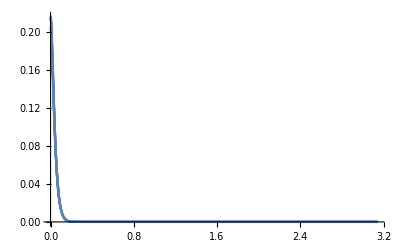

```mathematica
controlparams = {kp->2000, kv->2Sqrt[2000]};
Kp = kp*IdentityMatrix[6]/.controlparams;
Kv = kv*IdentityMatrix[6]/.controlparams;
(*Module for error dynamics*)
(*errordyn=NDSolve[{e''[t]+Kp.e[t]+Kv.e'[t]==0,e[0]==θdinit/3,e'[0]==dθdinit/3},e,{t,0,tf}][[1]];
*)
errordyn=NDSolve[{e''[t]+Kp.e[t]+Kv.e'[t]==0,e[0]==einit,e'[0]==deinit},e,{t,0,tf}, AccuracyGoal->25][[1]];
Plot[e[t]/.errordyn,{t, 0, tf}, PlotRange->All]
```

```mathematica
(*Now sampling the errors*)
```

```mathematica
edat = Table[e[t]/.errordyn, {t, 0, tf, h}];
dedat = Table[e'[t]/.errordyn, {t, 0, tf, h}];
```

```mathematica
(*Finding the second derivative of the desired joint angle values*)
```

```mathematica
tic[]
d2θddat = Table[d2x2d2qe[xtrackdat[[i]], dxtrackdat[[i]], d2xtrackdat[[i]]][[2]][[19;;24]],{i, Length[xtrackdat]}];
dθddat = Table[d2x2d2qe[xtrackdat[[i]], dxtrackdat[[i]], d2xtrackdat[[i]]][[1]][[19;;24]],{i, Length[xtrackdat]}];
toc[]
```

Actual time consumed: 2.089803 seconds.

CPU time consumed: 1.953 seconds.

```mathematica
τdash = Table[d2θddat[[i]]+Kp.edat[[i]]+Kv.dedat[[i]],{i, Length[edat]}];
```

```mathematica
(*Mapping τdash to the required torque values*)
```

```mathematica
θidat = θddat-edat;
dθidat = dθddat-dedat;
```

```mathematica
(*Initial condition for the other simulation*)
```

```mathematica
(*Since the matrices are all in extended configuration space we need the data for all the other variables also*)
```

```mathematica
tempinit = Join[xtrackdat[[1]], iksol[xtrackdat[[1]]]][[1;;18]];
qeidat = Table[tempinit = TrackRoot[θidat[[i]], tempinit];
Join[TrackRoot[θidat[[i]], tempinit], θidat[[i]]],{i, Length[θidat]}];
```

```mathematica
(*We need the first order data of all these variables*)
```

```mathematica
dqeidat = Table[qe2dqe[qeidat[[i]], dθidat[[i]]],{i, Length[dθidat]}];
```

```mathematica
tic[]
τvals = Table[findτ[qeidat[[i]], dqeidat[[i]], τdash[[i]]], {i, Length[qeidat]}];
toc[]
```

Actual time consumed: 1.958876 seconds.

CPU time consumed: 1.906 seconds.

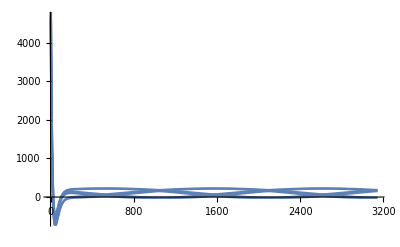

```mathematica
Show[Table[ListLinePlot[τvals[[;;, i]], PlotRange->All],{i,6}]]
```

```mathematica
cartacc = Table[d2xtrackdat[[i]][[1;;3]], {i, Length[d2xtrackdat]}];
```

```mathematica
(*Max cartesian accelerations*)
```

```mathematica
{Max[Abs[cartacc[[;;,1]]]], Max[Abs[cartacc[[;;,2]]]], Max[Abs[cartacc[[;;,3]]]]}
```

{1.2,1.2,0.}

```mathematica
(*So, these are the required torques from the feedback linearised model. We need to simulate it and validate it against the required data*)
```

```mathematica
(*Ideally the torques should be say in zero order hold until the next control loop. But here we fit an interpolation function to the torques*)
```

```mathematica
time = Table[i, {i, 0, tf, h}];
τvalswitht = Table[Transpose[ArrayFlatten[{time, τvals[[;;, i]]}]],{i, 6}];
τfuncs = Table[Interpolation[τvalswitht[[i]]],{i, 6}];
```

```mathematica
(*Now we have the torques at each instant, let us simulate the system with these inputs*)
```

```mathematica
tempxϕ = qeidat[[1]][[1;;18]];
doubledotscontrol[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&), t_]:=Module[{bla, Mval, Cval, Gval, LHS, dqe, qe, Jηxϕval,Jηθval,Jxϕθval,dJηxϕval,dJηθval,Jqeθval,dJqeθval,Mθval,Cθval,Gθval, τθval},
(*Perform FK for the configuration and task space variables*)
(*bla= AbsoluteTiming[TrackRoot[q, tempxϕ]];*)
(*Print[bla[[1]]];*)
(*tempxϕ = bla[[2]];*)
tempxϕ = TrackRoot[q, tempxϕ];
qe = Join[tempxϕ,q];
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dq, dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
τθval = {τfuncs[[1]][t], τfuncs[[2]][t], τfuncs[[3]][t], τfuncs[[4]][t], τfuncs[[5]][t], τfuncs[[6]][t]};
LHS = (Inverse[Mθval]).(τθval-Cθval.dq-Gθval);
Return[LHS];
];
```

```mathematica
θinitc = θidat[[1]];
dθinitc = dθidat[[1]];
```

```mathematica
d2θinitc = doubledotsac[θinitc, dθinitc]
```

{-7.61845,-7.09244,-9.31268,-9.31268,-7.09244,-7.61845}

```mathematica
(*Using ADAMS is taking a lot of time and hence removed it*)
```

```mathematica
tempxϕ = qeidat[[1]][[1;;18]];
tic[]
controlsim = NDSolve[{doubledotscontrol[q1[t],q1'[t],t]==q1''[t],q1[0]==θinitc,q1'[0]==dθinitc},q1,{t,0,tf}][[1]];
toc[]
```

InterpolatingFunction::dmval: Input value {3.14159} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Actual time consumed: 0.517704 seconds.

CPU time consumed: 0.438 seconds.

```mathematica
qcontrol = q1/.controlsim;
```

```mathematica
qcontroldat = Table[qcontrol[i],{i,0,tf,h}];
```

```mathematica
Clear[i];
tempinit = qeidat[[1]][[1;;18]];
qecdat = Table[tempinit = TrackRoot[qcontroldat[[i]], tempinit];
Join[TrackRoot[qcontroldat[[i]], tempinit], qcontroldat[[i]]],{i, Length[qcontroldat]}];
```

```mathematica
(*Now collect the {x,y,z} data*)
```

```mathematica
xcontroldat = Table[qecdat[[i]][[1;;3]],{i, Length[qecdat]}];
θcontroldat = Table[qecdat[[i]][[19;;24]],{i, Length[qecdat]}];
```

```mathematica
(*The actual path vs the tracked path*)
```

```mathematica
Show[ListPointPlot3D[xcontroldat, PlotStyle->Red], trackedpath]
```

-Graphics3D-

```mathematica
Manipulate[Show[plotsrspm[Inner[Rule, q, qecdat[[i]], List]], ListPointPlot3D[xcontroldat[[1;;i]], PlotStyle->Red]], {i, 1, Length[xcontroldat], 1}];
```

```mathematica
elist = xcontroldat-xtrackdat[[;;,1;;3]];
```

```mathematica
enorm = Table[Sqrt[elist[[i]].elist[[i]]],{i, Length[elist]}];
```

```mathematica
temperror = Table[{time[[i]],enorm[[i]]}, {i, Length[enorm]}];
```

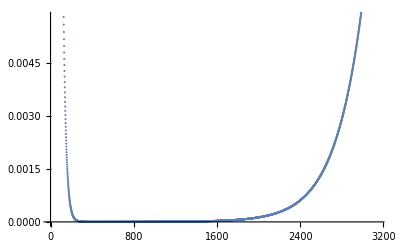

```mathematica
ListPlot[enorm]
```

```mathematica
bla = θcontroldat-θddat;
```

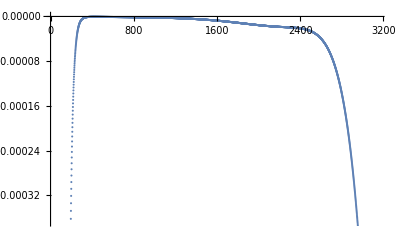

```mathematica
ListPlot[bla[[;;,6]]]
```

```mathematica
d2x2d2qe[qx_, dqx_, d2qx_]:= Module[{Jηqval, Jηxval, Jqxval, dJηqval, dJηxval, dqe, Jqexval, dJqexval, d2qeval, qe},
qe = Join[qx, iksol[qx]];
Jηqval = cJηq@@qe;
Jηxval = cJηx@@qe;
Jqxval = -Inverse[Jηqval].Jηxval;
dqe = Join[dqx, Jqxval.dqx];
(*Computing the derivative of the Jacobians*)
dJηqval = cdJηq@@Join[qe, dqe];
dJηxval = cdJηx@@Join[qe, dqe];
(*Map of the matrices*)
d2qeval = Join[d2qx,-Inverse[Jηqval].(dJηxval.dqx+Jηxval.d2qx+dJηqval.dqe[[7;;]])];
Return[{dqe, d2qeval}];
]
```

```mathematica
(*Having the error computation and the dynamics simulation in the same module*)
```

```mathematica
(*h = 0.001;
tf = π;*)
```

```mathematica
(*N[0.3*Sqrt[2]]*)
```

```mathematica
(*scale = 2;
xparam = xp*Sin[ωx*t-δx]/.{xp->.6/scale, ωx->2, δx->π/2};
yparam = yp*Sin[ωy*t-δy]/.{yp->.6/scale, ωy->2, δy->0};
zparam = 1;
trackedpath = ParametricPlot3D[{xparam, yparam, zparam},{t, 0,tf}, PlotStyle->Dashed]
xtrack = {xparam, yparam, zparam, 0,0,0};
dxtrack = D[{xparam, yparam, zparam, 0,0,0}, t];
d2xtrack = D[{xparam, yparam, zparam, 0,0,0}, {t, 2}];*)
```

```mathematica
(*(*Getting the task space desired data*)
xtrackdat = Table[N[xtrack/.{t->i}],{i, 0, tf, h}];
dxtrackdat = Table[N[dxtrack/.{t->i}],{i, 0, tf, h}];
d2xtrackdat = Table[N[d2xtrack/.{t->i}],{i, 0, tf,h}];*)
```

```mathematica
(*We assume that we are within the SWZ. We try to track a 3D-Lissajous Curve with no change in c1, c2, c3*)
scale = 1.5;
xparam = xp*Sin[ωx*t-δx]/.{xp->.6/scale, ωx->2, δx->π/2};
yparam = yp*Sin[ωy*t-δy]/.{yp->.3/scale, ωy->8, δy->0};
zparam = 1+zp*Sin[ωz*t-δz]/.{zp->.2/scale, ωz->4, δz->π/2};
trackedpath = ParametricPlot3D[{xparam, yparam, zparam},{t, 0,π}, PlotStyle->Dashed]
xtrack = {xparam, yparam, zparam, 0,0,0};
dxtrack = D[{xparam, yparam, zparam, 0,0,0}, t];
d2xtrack = D[{xparam, yparam, zparam, 0,0,0}, {t, 2}];
```

-Graphics3D-

```mathematica
tf = π
```

π

```mathematica
(*Getting the task space desired data*)
xtrackdat = Table[N[xtrack/.{t->i}],{i, 0, tf, h}];
dxtrackdat = Table[N[dxtrack/.{t->i}],{i, 0, tf, h}];
d2xtrackdat = Table[N[d2xtrack/.{t->i}],{i, 0, tf,h}];
```

```mathematica
(*h = 0.001;
tside =1;
tf = 4;
side = 0.5;
height = 1;
s1 = Table[{side,side, height,0,0,0}*(tside-t)/tside+{-side,side, height,0,0,0}*t/tside,{t, 0, tside,h}];
ds1 = Table[{-2*side,0,0,0,0,0},{t, 0, tside,h}];
s2 = Table[{-side,side, height,0,0,0}*(tside-t)/tside+{-side, -side, height,0,0,0}*t/tside,{t, 0, tside,h}];
ds2 = Table[{0,-2*side,0,0,0,0},{t, 0, tside,h}];
s3 = Table[{-side, -side, height,0,0,0}*(tside-t)/tside+{side, -side, height,0,0,0}*t/tside,{t, 0, tside,h}];
ds3 = Table[{2*side,0,0,0,0,0},{t, 0, tside,h}];
s4 = Table[{side, -side, height,0,0,0}*(tside-t)/tside+{side, side, height,0,0,0}*t/tside,{t, 0, tside,h}];
ds4 = Table[{0,2*side,0,0,0,0},{t, 0, tside,h}];*)
```

```mathematica
(*(*Getting the task space desired data*)
xtrackdat = Join[s1, s2[[2;;]], s3[[2;;]], s4[[2;;]]];
dxtrackdat = Join[ds1, ds2, ds3, ds4];
d2xtrackdat = ConstantArray[0, Dimensions[xtrackdat]];*)
```

```mathematica
(*trackedpath = ListPointPlot3D[xtrackdat[[;;,1;;3]]]*)
```

-Graphics3D-

```mathematica
tic[]
qddat = Table[iksol[xtrackdat[[i]]],{i, Length[xtrackdat]}];
θddat = qddat[[;;, 13;;18]];
d2θddat = Table[d2x2d2qe[xtrackdat[[i]], dxtrackdat[[i]], d2xtrackdat[[i]]][[2]][[19;;24]],{i, Length[xtrackdat]}];
dθddat = Table[d2x2d2qe[xtrackdat[[i]], dxtrackdat[[i]], d2xtrackdat[[i]]][[1]][[19;;24]],{i, Length[xtrackdat]}];
toc[]
```

Actual time consumed: 1.755997 seconds.

CPU time consumed: 1.75 seconds.

```mathematica
(*Converting the discrete data into an interpolation function*)
time = Table[t, {t, 0 ,tf, h}];
tempref =Transpose[ArrayFlatten[{time, θddat}]];
tempdref =Transpose[ArrayFlatten[{time, dθddat}]];
tempd2ref =Transpose[ArrayFlatten[{time, d2θddat}]];
θref=Interpolation[tempref];
dθref=Interpolation[tempdref];
d2θref=Interpolation[tempd2ref];
```

```mathematica
controlparams = {kp->2000, kv->2Sqrt[2000]};
Kp = kp*IdentityMatrix[6]/.controlparams;
Kv = kv*IdentityMatrix[6]/.controlparams;
```

```mathematica
controlinput = {};
```

```mathematica
tempxϕ = qeidat[[1]][[1;;18]];
controlandsim[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&), t_]:=Module[{bla, Mval, Cval, Gval, LHS, dqe, qe, Jηxϕval,Jηθval,Jxϕθval,dJηxϕval,dJηθval,Jqeθval,dJqeθval,Mθval,Cθval,Gθval, τθval,dθival,θival,edat,dedat,τdash},
(*Perform FK for the configuration and task space variables*)
tempxϕ = TrackRoot[q, tempxϕ];
qe = Join[tempxϕ,q];
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dq, dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
edat = θref[t] - q;
dedat = dθref[t] - dq;
τdash = d2θref[t]+Kp.edat+Kv.dedat;
τθval = (Mθval.τdash)+Cθval.dq+Gθval;
(*LHS = (Inverse[Mθval]).(τθval-Cθval.dq-Gθval);*)
LHS = τdash;
AppendTo[controlinput, τθval];
(*Print[{edat, dedat, dq}];*)
Return[LHS];
];
```

```mathematica
tempxϕ = qeidat[[1]][[1;;18]];
tic[]
controlsim = NDSolve[{controlandsim[q1[t],q1'[t],t]==q1''[t],q1[0]==θinitc,q1'[0]==dθinitc},q1,{t,0,tf}][[1]];
toc[]
```

InterpolatingFunction::dmval: Input value {3.14159} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction::dmval will be suppressed during this calculation.

Actual time consumed: 1.564106 seconds.

CPU time consumed: 1.469 seconds.

```mathematica
(*StepDataPlot[controlsim]/.AbsolutePointSize[_]->PointSize[Small]*)
```

```mathematica
(*Max actuator requirements*)
Table[Max[controlinput[[;;,i]]],{i, 6}]
```

{500.539,7387.02,1362.63,454.995,8891.82,4504.27}

```mathematica
(*Default image size is 800*)
Texplot[xaxis_, yaxis_, imgsize_, xlabel_, ylabel_]:=Module[{magni1, fontsize, markersize, color, markers, flist, f1nonsing},
magni1=2; (*Magnification in axis and axis labesl*)
fontsize=20; (*Axis font label size*)
markersize=20; 
color={Directive[RGBColor[0,0,1]],Directive[Orange],Directive[Red],Directive[Brown],Directive[RGBColor[0.5,0.5,0]],Directive[RGBColor[0,0.6,0]]};
markers={{"+",markersize},{"○",markersize},{"△",markersize},{"□",markersize},{"♢",markersize},{"*",markersize}};

flist=Table[{xaxis[[i]],yaxis[[i]]},{i,1,Length[xaxis],1}];

f1nonsing=ListPlot[{flist},PlotRange->Automatic,BaseStyle->{FontFamily->"Latin Modern Roman"},Frame->True,FrameStyle->{Directive[Black,fontsize],Directive[Black,fontsize]},GridLines->Automatic,PlotStyle->color,PlotMarkers->markers[[1]],FrameLabel->{MaTeX[ToString["\\text{"<>xlabel<>"}"],Magnification->magni1],MaTeX[ToString[ylabel],Magnification->magni1]},Joined->True, ImageSize->imgsize, PlotRange->All];

Return[f1nonsing];
]
```

```mathematica
(*Texplot[time, ηtest*10^16, 800, "Time~(s)", "e_1 (\\times 10^{-16})"]*)
```

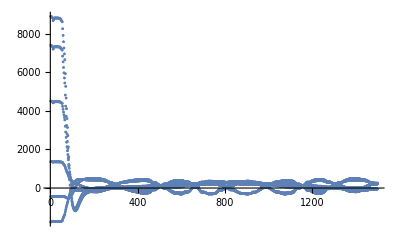

```mathematica
Show[Table[ListPlot[controlinput[[;;, i]]], {i, 6}], PlotRange->All]
```

```mathematica
qcontrol = q1/.controlsim;
qcontroldat = Table[qcontrol[i],{i,0,tf,h}];
```

```mathematica
Clear[i];
tempinit = qeidat[[1]][[1;;18]];
qecdat = Table[tempinit = TrackRoot[qcontroldat[[i]], tempinit];
Join[TrackRoot[qcontroldat[[i]], tempinit], qcontroldat[[i]]],{i, Length[qcontroldat]}];
xcontroldat = Table[qecdat[[i]][[1;;3]],{i, Length[qecdat]}];
θcontroldat = Table[qecdat[[i]][[19;;24]],{i, Length[qecdat]}];
```

```mathematica
(*The actual path vs the tracked path*)
Show[{ListPointPlot3D[xcontroldat, PlotStyle->Red, PlotRange->All], trackedpath}, PlotRange->All, AxesLabel->{"x-axis", "y-axis", "z-axis"}, PlotLabel->"Following a rectangular path", ImageResolution->600, ImageSize->Full, PlotLegends->Automatic, AxesStyle->Directive[Black, 20], LabelStyle->Directive[Black,20]]
```

-Graphics3D-

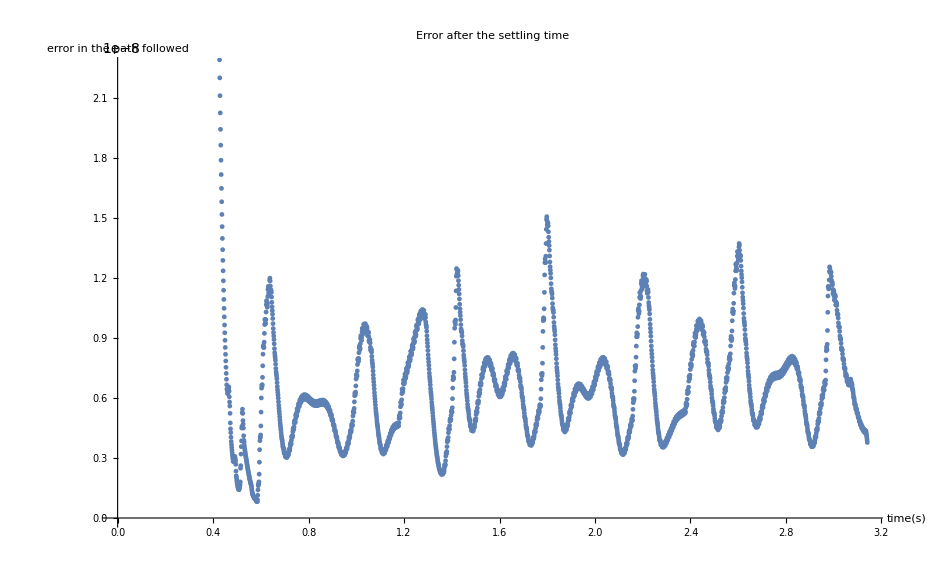

```mathematica
elist = xcontroldat-xtrackdat[[;;,1;;3]];
enorm = Table[Sqrt[elist[[i]].elist[[i]]],{i, Length[elist]}];
tempelist = Table[{time[[i]], enorm[[i]]},{i, Length[time]}];
ListPlot[tempelist, PlotLabel->"Error after the settling time",AxesLabel->{"time(s)", "error in the path followed"},  AxesStyle->Directive[Black, 20], LabelStyle->Directive[Black,20],  PlotStyle->Thick]
```

```mathematica
(*temperror = Table[{time[[i]],enorm[[i]]}, {i, Length[enorm]}];
ListPlot[temperror]*)
```

```mathematica
Eigenvalues[ArrayFlatten[{{ConstantArray[0,{6,6}],IdentityMatrix[6]},{-Kp,-Kv}}]]
```

{-20 √5,-20 √5,-20 √5,-20 √5,-20 √5,-20 √5,-20 √5,-20 √5,-20 √5,-20 √5,-20 √5,-20 √5}

```mathematica
errorth = Table[θddat[[;;,i]]-θcontroldat[[;;,i]],{i, 6}];
```

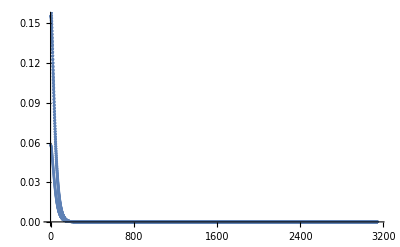

```mathematica
Show[Table[ListPlot[errorth[[i]], PlotRange->All],{i, 6}]]
```

```mathematica
Manipulate[Show[plotsrspm[Inner[Rule, q, qecdat[[i]], List]], ListPointPlot3D[xcontroldat[[1;;i]], PlotStyle->Red]], {i, 1, Length[xcontroldat], 1}]
```

```mathematica
qecdat//Dimensions
```

{3142,24}

```mathematica
(*frames = Table[Export["liss"<>ToString[j/10]<>".jpeg", Show[plotsrspm[Inner[Rule, q, qecdat[[i]], List]], ListPointPlot3D[xcontroldat[[1;;i]], PlotStyle->Red]]],{j, 10, 3142, 10}];*)
```

```mathematica
(*Table[t, {t, 10, 3142, 10}]*)
```

{10,20,30,40,50,60,70,80,90,100,110,120,130,140,150,160,170,180,190,200,210,220,230,240,250,260,270,280,290,300,310,320,330,340,350,360,370,380,390,400,410,420,430,440,450,460,470,480,490,500,510,520,530,540,550,560,570,580,590,600,610,620,630,640,650,660,670,680,690,700,710,720,730,740,750,760,770,780,790,800,810,820,830,840,850,860,870,880,890,900,910,920,930,940,950,960,970,980,990,1000,1010,1020,1030,1040,1050,1060,1070,1080,1090,1100,1110,1120,1130,1140,1150,1160,1170,1180,1190,1200,1210,1220,1230,1240,1250,1260,1270,1280,1290,1300,1310,1320,1330,1340,1350,1360,1370,1380,1390,1400,1410,1420,1430,1440,1450,1460,1470,1480,1490,1500,1510,1520,1530,1540,1550,1560,1570,1580,1590,1600,1610,1620,1630,1640,1650,1660,1670,1680,1690,1700,1710,1720,1730,1740,1750,1760,1770,1780,1790,1800,1810,1820,1830,1840,1850,1860,1870,1880,1890,1900,1910,1920,1930,1940,1950,1960,1970,1980,1990,2000,2010,2020,2030,2040,2050,2060,2070,2080,2090,2100,2110,2120,2130,2140,2150,2160,2170,2180,2190,2200,2210,2220,2230,2240,2250,2260,2270,2280,2290,2300,2310,2320,2330,2340,2350,2360,2370,2380,2390,2400,2410,2420,2430,2440,2450,2460,2470,2480,2490,2500,2510,2520,2530,2540,2550,2560,2570,2580,2590,2600,2610,2620,2630,2640,2650,2660,2670,2680,2690,2700,2710,2720,2730,2740,2750,2760,2770,2780,2790,2800,2810,2820,2830,2840,2850,2860,2870,2880,2890,2900,2910,2920,2930,2940,2950,2960,2970,2980,2990,3000,3010,3020,3030,3040,3050,3060,3070,3080,3090,3100,3110,3120,3130,3140}

```mathematica
(*(*Writing the control conputation and system simulation seperately*)
(*Module to find the torque at the sampled instant*)
computecontrol[qe_, dqe_, t_]:=Module[{Mval, Cval, Gval, LHS,Jηxϕval,Jηθval,Jxϕθval,dJηxϕval,dJηθval,Jqeθval,dJqeθval,Mθval,Cθval,Gθval, τθval,dθival,θival,edat,dedat,τdash, tempdθ,tempθ},
tempdθ = dqe[[19;;24]];
tempθ = qe[[19;;24]];
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
edat = θref[t] - tempθ;
dedat = dθref[t] - tempdθ;
τdash = d2θref[t]+Kp.edat+Kv.dedat;
τθval = (Mθval.τdash)+Cθval.tempdθ+Gθval;
Return[τθval];
];*)
```

```mathematica
(*config = ConstantArray[0,{24}];
dconfig = ConstantArray[0,{24}];*)
```

```mathematica
(*tempxϕ = qeidat[[1]][[1;;18]];
systemsim[q_?(VectorQ[#,NumericQ]&),dq_?(VectorQ[#,NumericQ]&), τθval_]:=Module[{bla, Mval, Cval, Gval, LHS, dqe, qe, Jηxϕval,Jηθval,Jxϕθval,dJηxϕval,dJηθval,Jqeθval,dJqeθval,Mθval,Cθval,Gθval, dθival,θival,edat,dedat,τdash},
(*Perform FK for the configuration and task space variables*)
tempxϕ = TrackRoot[q, tempxϕ];
qe = Join[tempxϕ,q];
(*Getting the velocities of the configuration space variables*)
Jηxϕval = cJηxϕ@@qe;
Jηθval = cJηθ@@qe;
Jxϕθval = -Inverse[Jηxϕval].Jηθval;
dqe = Join[Jxϕθval.dq, dq];
(*Compute all the extended configuration space matrices*)
Mval=cMmat@@qe;
Cval=cCmat@@Join[qe, dqe];
Gval=cGvec@@qe;
(*Computing the derivative of the Jacobians*)
dJηxϕval = cdJηxϕ@@Join[qe, dqe];
dJηθval = cdJηθ@@Join[qe, dqe];
(*Map of the matrices*)
Jqeθval = ArrayFlatten[{{Jxϕθval}, {IdentityMatrix[6]}}];
dJqeθval = ArrayFlatten[{{-Inverse[Jηxϕval].(-dJηxϕval.Inverse[Jηxϕval].Jηθval+dJηθval)}, {ConstantArray[0,{6,6}]}}];
(*Map the matrices to the task space*)
Mθval = T[Jqeθval].Mval.Jqeθval;
Cθval = T[Jqeθval].(Mval.dJqeθval+Cval.Jqeθval);
Gθval = T[Jqeθval].Gval;
(*LHS of the dynamics equations*)
(*τθval = computecontrol[qe, dqe, t];*)
LHS = (Inverse[Mθval]).(τθval-Cθval.dq-Gθval);
(*AppendTo[controlinput, τθval];*)
config = qe;
dconfig = qe;
Return[LHS];
];*)
```

```mathematica
(*(*Control is computed for every 0.1 s*)
tsys = 0.001;
(*config = {-0.30769230769230765,-2.8695760407488136*^-17,0.6666666666666666,-4.298758185320587*^-19,5.2967228549980035*^-17,-3.05834777340713*^-17,-0.6468727353940114,-0.7396108756073955,0.27582767997240515,0.275827679972405,-0.7396108756073954,-0.6468727353940111,0.5034118398526536,0.4168936722236682,-0.08704971895328104,0.08704971895328126,-0.4168936722236683,-0.5034118398526536,0.953774282357119,0.9869825161206649,0.6954899933969605,0.6954899933969606,0.9869825161206648,0.953774282357119};
*)
config = Join[xtrackdat[[1]], iksol[xtrackdat[[1]]]];
dconfig = ConstantArray[0, {24}];
tempxϕ = qeidat[[1]][[1;;18]];
states = {};*)
```

```mathematica
(*For[i=0, i≤1000, i++,
θi = config[[19;;24]];
dθi = dconfig[[19;;24]];
AppendTo[states, {config, dconfig}];
τθval = computecontrol[config,dconfig,i*tsys];
NDSolve[{systemsim[q1[t],q1'[t],t]==q1''[t],q1[0]==θi,q1'[0]==dθi},q1,{t,0,tsys}][[1]];
]*)
```

```mathematica
(*bla = states[[;;,1,;;]];*)
```

```mathematica
(*xvals = Table[bla[[i]][[1;;3]],{i, Length[bla]}];*)
```

```mathematica
(*ListPointPlot3D[xvals]*)
```